# DOD = 1 Triangle subtraction example

## Tooling

```mathematica
SetAttributes[SP4,Orderless];
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
Needs["cLTD`",NotebookDirectory[]<>"cLTD/cLTD.m"]
```

```mathematica
FORMPATH="/Users/vjhirsch/HEP_programs/form/bin/form";
```

```mathematica
SetOptions[cLTD,
	"WorkingDirectory"->NotebookDirectory[]<>"cLTD_work_dir/",
	"FORMpath"->FORMPATH,
	"FORM_ID"->1]//TableForm
SetOptions[GeneratecLTDExpression,
	"WorkingDirectory"->NotebookDirectory[]<>"cLTD_work_dir/",
	"FORMpath"->FORMPATH,
	"FORM_ID"->1];
```

loopmom→{k0,k1,k2,k3}
FORMpath→/Users/vjhirsch/HEP_programs/form/bin/form
tFORMpath→tform
WorkingDirectory→/Users/vjhirsch/Documents/Work/Projects/alphaLoop/git_alphaLoopMisc/UV_derivatives_with_CFF_final/DOD1_example/cLTD_work_dir/
FORM_ID→1
FORMcores→1
OptimizationLVL→0
keep_FORM_script→False
EvalAll→False
NoNumerator→False
FORMsubs→False
stdLTD→False

```mathematica
ClearAll[GenerateLMBData];
GenerateLMBData[g_,OptionsPattern[{loopshift->{},externalshift->{}}]]:=Module[
{
edges=EdgeList[g],
props,
shift,
lmbEdgesIDs=Table[(e/.DirectedEdge[_,_,props_]:>props)["id"],{e,cFFGetLMBEdges[g]}],
externals=cFFGetExternalEdges[g]
},
Association[Table[
props=(e/.DirectedEdge[_,_,props_]:>props);
shift=If[AllTrue[props["sig"]⟦1⟧,(#===0)&],
OptionValue[externalshift]
,
OptionValue[loopshift]
];
props["id"]-><|
"mass"->props["mass"],
"lmb_decomposition"->(
(
((props["sig"]⟦1⟧.Table[q[i],{i,lmbEdgesIDs}])
+(props["sig"]⟦2⟧.Table[q[(e/.DirectedEdge[_,_,props_]:>props)["id"]],{e,externals}]))/.shift
)
)
|>
,{e,edges}
]]
]
```

```mathematica
GetVirtualPropagators[g_]:=Module[
{
externalIDs=Table[(e/.DirectedEdge[_,_,props_]:>props)["id"],{e,cFFGetExternalEdges[g]}]
},
Select[EdgeList[g],Not[MemberQ[externalIDs,(#/.DirectedEdge[_,_,props_]:>props)["id"]]]&]
]
```

```mathematica
GetVirtualPropagatorsIDs[g_]:=
Table[(e/.DirectedEdge[_,_,props_]:>props)["id"],{e,GetVirtualPropagators[g]}]
```

```mathematica
ExpandSP4[Num_]:=TensorExpand[Num/.{SP4[a_,b_]:>Cross[a/.{v_[i_]:>L[v[i]]},b/.{v_[i_]:>R[v[i]]}]}]/.{Cross[L[a_],R[b_]]:>SP4[a,b]}
```

```mathematica
NorExactZero[expr_]:=If[Evaluate[FullSimplify[expr]]===0,0,N[expr]]
```

```mathematica
ClearAll[ComputeSubtractionTermFromNormalized];
ComputeSubtractionTermFromNormalized[ct_,numerics_]:=Module[{lmbEdges,orkey,sortedEdgeIDs,reducedGraph,reducedGraphEdgeList,externalEdges,g},
lmbEdges=cFFGetLMBEdges[ct["graph"]];
g=ct["graph"];
externalEdges=cFFGetExternalEdges[g];
reducedGraph=GraphDifference[g,DirectedGraph[externalEdges]];
reducedGraphEdgeList=EdgeList[reducedGraph];
sortedEdgeIDs=Sort[Table[(e/.{DirectedEdge[_,_,props_]:>props})["id"],{e,GetVirtualPropagators[ct["graph"]]}]];
Association[SortBy[Table[
orkey=Table[
orientation["Orientation"][eID],
{eID,sortedEdgeIDs}
];
orkey->
1/(-1)^Length[reducedGraphEdgeList](-1)^Length[sortedEdgeIDs]/(-I)^Length[lmbEdges](1/λ)^3 EvalcFF[
ct["graph"],
{orientation},
numerics/.{Rule[k1,a_]->Rule[k1,1/λ a]},
Num->ct["num"],
DEBUG->False]
,
{orientation,ct["cFFexpr"]}],(#⟦1⟧)&]
]]
```

```mathematica
ClearAll[ComputeSubtractionTerm];
ComputeSubtractionTerm[ct_,numerics_,OptionsPattern[{UVEdgeIDs->{},UVTscalingReplacements->{},NumeratorFudge->None, DebugNumerator->False, UVRescaling->True}]]:=Module[
{orkey,sortedEdgeIDs,scalednumerics,ResPerOrientations,OSEReplacement,ShiftsReplacement,lmbEdges,externalEdges,g,orientationsForThisTerm,
signatures,momLabels,reducedGraph,reducedGraphEdgeList,processedNum, numForThisOrientation,internalOSEs,normalization,tmpKey,resForThisOrientation,OSEDef},
g=ct["graph"];
sortedEdgeIDs=Sort[Table[(e/.{DirectedEdge[_,_,props_]:>props})["id"],{e,GetVirtualPropagators[g]}]];
scalednumerics=If[OptionValue[UVRescaling],
numerics/.{Rule[k1,a_]->Rule[k1,1/λ a]},
numerics
];
momLabels=cFFGenerateMomentaLabels[g];
signatures=Association[Table[((#["id"]->#["sig"])&)[e/.{DirectedEdge[_,_,props_]:>props}],{e,EdgeList[g]}]];

lmbEdges=cFFGetLMBEdges[g];
externalEdges=cFFGetExternalEdges[g];
reducedGraph=GraphDifference[g,DirectedGraph[externalEdges]];
reducedGraphEdgeList=SortBy[EdgeList[reducedGraph],(Evaluate[(#/.{DirectedEdge[_,_,props_]:>props})]["id"])&];
ShiftsReplacement = Table[pE[iExt]:>Evaluate[ToExpression["p"<>ToString[iExt]<>"E"]],{iExt,Length[externalEdges]}]/.numerics;

processedNum=TensorExpand[ct["num"]/.{SP4[a_,b_]:>Cross[a/.{v_[i_]:>L[v[i]]},b/.{v_[i_]:>R[v[i]]}]}]/.{Cross[L[a_],R[b_]]:>SP4[a,b]};
processedNum=(processedNum/.{SP4[a_,b_]:>(a[0]*b[0]-a . b)})/.{q[i_][0]:>qE[i]};
Do[
processedNum=(((processedNum)/.{q[uveid]:>(signatures[uveid][[1]] . momLabels[[1]]+signatures[uveid][[2]] . momLabels[[2]])})/.Table[qE[(externalEdges[[iExt]]/.{DirectedEdge[_,_,props_]:>props})["id"]]:>Evaluate[pE[iExt]],{iExt,Length[externalEdges]}]);
processedNum=processedNum/.ShiftsReplacement;
,{uveid,OptionValue[UVEdgeIDs]}
];

processedNum=processedNum/.OptionValue[UVTscalingReplacements];
processedNum=(((processedNum)/.{q[i_]:>(signatures[i][[1]] . momLabels[[1]]+signatures[i][[2]] . momLabels[[2]])})/.Table[qE[(externalEdges[[iExt]]/.{DirectedEdge[_,_,props_]:>props})["id"]]:>Evaluate[pE[iExt]],{iExt,Length[externalEdges]}]);

If[OptionValue[DebugNumerator],
Print["Numerator:"];
Print[processedNum];
];
If[Not[OptionValue[NumeratorFudge]===None],
processedNum=OptionValue[NumeratorFudge][processedNum];
If[OptionValue[DebugNumerator],
Print["Numerator after fudge:"];
Print[processedNum];
];
];

processedNum=processedNum/.ShiftsReplacement;
processedNum=processedNum/.scalednumerics;

OSEReplacement=If[
Length[scalednumerics]==0,
{},
ComputeOSEReplacements[g,{}]
];
OSEReplacement=Table[
OSEDef=If[
MemberQ[OptionValue[UVEdgeIDs],eID],
((OSE[eID]/.OSEReplacement)/.OptionValue[UVTscalingReplacements])/.scalednumerics,
(OSE[eID]/.OSEReplacement)/.scalednumerics
];
OSE[eID]->OSEDef,
{eID,sortedEdgeIDs}
];

(*Print[OSEReplacement];*)
normalization=( (*(-I)^Length[lmbEdges]*)1/ ((Times@@Table[-2*OSE[(e/.{DirectedEdge[_,_,props_]:>props})["id"]],{e,EdgeList[reducedGraph]}])) );

Association[SortBy[Table[
(*
orkey=Table[
If[o,-1,1],
{o,orientation⟦1⟧}
];
*)
(*
orkey=Table[
tmpKey=Evaluate[(e/.{DirectedEdge[_,_,props_]:>props})]["id"];
orientation⟦1⟧[tmpKey],
{e,reducedGraphEdgeList}
];
*)
orkey=Table[
orientation⟦1⟧[eID],
{eID,sortedEdgeIDs}
];

orientationsForThisTerm=Association[Table[
tmpKey=Evaluate[(reducedGraphEdgeList⟦ie⟧/.{DirectedEdge[_,_,props_]:>props})]["id"];
tmpKey->orkey⟦ie⟧,{ie,Length[reducedGraphEdgeList]}]];

numForThisOrientation=(processedNum/.Table[qE[edgeID]->(orientationsForThisTerm[edgeID]*OSE[edgeID]),{edgeID,Keys[orientationsForThisTerm]}]);

resForThisOrientation=If[OptionValue[UVRescaling],(1/λ)^3,1]*((normalization orientation⟦2⟧)/.scalednumerics);
resForThisOrientation=((resForThisOrientation/.OptionValue[UVTscalingReplacements])*numForThisOrientation);
If[MemberQ[Keys[ct],"dots"],
Do[
Do[
resForThisOrientation=1/(2OSE[d])D[resForThisOrientation,OSE[d]]
,{id,ct["dots"][d]-1}];
resForThisOrientation=resForThisOrientation/Gamma[ct["dots"][d]]
,{d,Keys[ct["dots"]]}];
];

resForThisOrientation=resForThisOrientation/.OSEReplacement;
orkey->resForThisOrientation
,
{orientation,ct["cFFexpr"]}],(#⟦1⟧)&]
]
]
```

```mathematica
(*ComputeSubtractionTerm[
<|
"num"->(SubtractionContribs["λ0CTDNumNoDot"]⟦1⟧["num"]/.UVExternalsDefinition),
"cFFexpr"->SubtractionContribs["λ0CTDNumNoDot"]⟦1⟧["cFFexpr"],
"graph"->SubtractionContribs["λ0CTDNumNoDot"]⟦1⟧["graph"],
"dots"->SubtractionContribs["λ0CTDNumNoDot"]⟦1⟧["dots"]
|>,subtractionNumerics
(*,NumeratorFudge->((Coefficient[#,(p[3][0])^2](p[3][0])^2)&)*)
][{-1,-1,-1,-1,-1,1}]*)
```

```mathematica
(*ComputeSubtractionTerm[CFFIntegrandForUVExpansion,TriBox1LParameters,UVEdgeIDs->Join[UVPropagatorsTriBox1L,{0,1,2,3,4,9}],UVTscalingReplacements->TriBox1LParametersForUVExpansion][{-1,-1,-1,-1,1,-1}]*)
```

```mathematica
IRes=ComputeSubtractionTerm[SubtractionData["I"],TriBox1Lnumerics];
```

```mathematica
ConvertCFFFormat[structuredCFF_,g_]:=Module[
{externalEdges,ShiftsReplacement,reducedGraph,flipConfiguration,tmpOrientation,momLabels},
externalEdges=cFFGetExternalEdges[g];
reducedGraph=GraphDifference[g,DirectedGraph[externalEdges]];

ShiftsReplacement = Table[pE[iExt]:>Evaluate[ToExpression["p"<>ToString[iExt]<>"E"]],{iExt,Length[externalEdges]}];
momLabels=cFFGenerateMomentaLabels[g];

SortBy[Table[
flipConfiguration=Association[Table[
tmpOrientation=o["Orientation"][Evaluate[(e/.{DirectedEdge[_,_,props_]:>props})]["id"]];
e->tmpOrientation,{e,EdgeList[reducedGraph]}]];
{
Association[Table[ok->o["Orientation"][ok],{ok,Sort[Keys[o["Orientation"]]]}]],

Total[Table[
1/Times@@Table[
es["overall_sign"]*(
Total[Table[OSE[ose],{ose,es["OSE"]}]]+
(cFFGenerateEnergyShiftSignatureForEsurf[g,es["OSE"],flipConfiguration].Table[ToExpression[ToString[p]<>"E"],{p,momLabels⟦2⟧}])/.ShiftsReplacement
)
,{es,t["Esurfs"]}
],{t,o["Terms"]}]]
}
,{o,structuredCFF}],(#⟦1⟧)&]
]
```

```mathematica
ClearAll[AnalyzeSubtraction];
AnalyzeSubtraction[Ires_,SubtractionRes_,lambdaTerm_,OptionsPattern[{fudges-><||>,ExpansionDepth->0,SelectedOrientations->Null}]]:=Module[
{tmpI,tmpCTs,sumCTs,res, selectedOs,tmpR},
(*
fudges=<|
"NumExpansion"->{1},
"NumDOSEDot"->{1,1,1},
"CFFDOSEDot"->{1,1,1}
|>;
*)
If[OptionValue["SelectedOrientations"]===Null,
selectedOs=Keys[Ires],
selectedOs=Select[Keys[Ires],MemberQ[OptionValue["SelectedOrientations"],#]&]
];
res=Table[
tmpI=SeriesCoefficient[Series[Ires[o],{λ,0,OptionValue["ExpansionDepth"]},Assumptions->λ>0],lambdaTerm]/.{Missing[x__]:>0};
tmpCTs=Association[
Table[
k->Table[
If[MemberQ[Keys[OptionValue["fudges"]],k],OptionValue["fudges"][k]⟦is⟧,1]
*If[
MemberQ[Keys[SubtractionRes[k]⟦is⟧],o],
If[
SubtractionRes[k]⟦is⟧[o]===0,
0,
tmpR=Series[SubtractionRes[k]⟦is⟧[o],{λ,0,OptionValue["ExpansionDepth"]},Assumptions->λ>0];
If[Normal[tmpR]===0,
0,
SeriesCoefficient[tmpR,lambdaTerm]/.{Missing[x__]:>0}
]
],
0
]
,{is,Length[SubtractionRes[k]]}],{k,Keys[SubtractionRes]}]];
sumCTs=FullSimplify[Total[Table[Total[tmpCTs[k]],{k,Keys[tmpCTs]}]]];
Join@@{
{o},
{ NorExactZero[tmpI],NorExactZero[-sumCTs],NorExactZero[tmpI-sumCTs]},
Flatten[Table[NorExactZero[tmpCTs[k]],{k,Keys[tmpCTs]}]]
}
,{o,selectedOs}
];
res=Join[{Join@@{
{"orientation","I","-SumCT","I-SumCT"},
Flatten[Table[Table[k<>"#"<>ToString[ik],{ik,Length[tmpCTs[k]]}],{k,Keys[tmpCTs]}]]
}},res];
AppendTo[res,Join[{"TOTAL"},
Table[
Total[Table[r⟦ri⟧,{r,res⟦2;;⟧}]],
{ri,2,Length[res⟦1⟧]}
]
]]
]
```

## Test Triangle

### Input

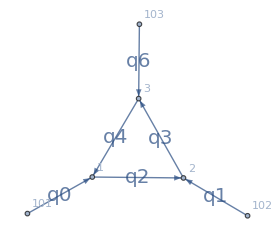

```mathematica
Tri1L=DirectedGraph[{
DirectedEdge[101,1,0],
DirectedEdge[102,2,1],
DirectedEdge[1,2,2],
DirectedEdge[2,3,3],
DirectedEdge[3,1,4],
DirectedEdge[103,3,6]
},VertexLabels->Automatic,EdgeLabels->Automatic];
Tri1L=AssignSignatures[Tri1L,masses-><|2->1,3->2,4->3|>,lmb->{3}];
Tri1L=DirectedGraph[Tri1L,VertexLabels->Automatic,ImageSize->275,GraphLayout->"HighDimensionalEmbedding",
EdgeLabels->Table[e->Style[("q"<>ToString[((e/.{DirectedEdge[_,_,props_]:>props})["id"])]),FontSize->20],{e,EdgeList[Tri1L]}]]
```

```mathematica
lmbVec=q[cFFGetLMBEdges[Tri1L]⟦1⟧/.{DirectedEdge[_,_,props_]:>props["id"]}];
```

```mathematica
Dataset[GenerateLMBData[Tri1L,loopshift->{q[0]:>(-q[1]-q[6])}]]
```

```mathematica
lmbData=GenerateLMBData[Tri1L,loopshift->{q[0]:>(-q[1]-q[6])}];
lmbDataLambda=Association[Table[k-><|
"mass"->λ lmbData[k]["mass"],"lmb_decomposition"->Simplify[λ (lmbData[k]["lmb_decomposition"]/.{lmbVec->1/λ lmbVec})]|>,
{k,Keys[lmbData]}]]
```

<|0→<|mass→0,lmb_decomposition→λ q[0]|>,1→<|mass→0,lmb_decomposition→λ q[1]|>,2→<|mass→λ,lmb_decomposition→-λ q[1]+q[3]|>,3→<|mass→2 λ,lmb_decomposition→q[3]|>,4→<|mass→3 λ,lmb_decomposition→q[3]+λ q[6]|>,6→<|mass→0,lmb_decomposition→λ q[6]|>|>

```mathematica
Tri1Lnumerics=GenerateRandomSample[Tri1L,Seed->1]
```

{k1→{2/3,3/5,5/7},p1→{7/11,11/13,13/17},p2→{17/19,19/23,23/29},p1E→29/31,p2E→31/37,p3→{-320/209,-500/299,-768/493},p3E→-2034/1147}

See how some small off-shellness in the external violates the subtraction

```mathematica
(* Tri1Lnumerics=Join[Tri1Lnumerics⟦;;-2⟧,{p3E->Evaluate[(p3E/.Tri1Lnumerics)]+1/3}] *)
```

```mathematica
subtractionNumerics=Join[
Tri1Lnumerics,
{mUV->10,
p[1][0]->(p1E/.Tri1Lnumerics),p[2][0]->(p2E/.Tri1Lnumerics),p[3][0]->(p3E/.Tri1Lnumerics),
p[1]->(p1/.Tri1Lnumerics),p[2]->(p2/.Tri1Lnumerics),p[3]->(p3/.Tri1Lnumerics)
}];
```

```mathematica
UVExternalsDefinition=Block[
{
externalEdges,externalEdgesIDs,momLabels,signatures
},
externalEdges=cFFGetExternalEdges[Tri1L];
externalEdgesIDs=Table[Evaluate[(ee/.{DirectedEdge[_,_,props_]:>props})]["id"],{ee,externalEdges}];
momLabels=cFFGenerateMomentaLabels[Tri1L];
signatures=Association[Table[((#["id"]->#["sig"])&)[e/.{DirectedEdge[_,_,props_]:>props}],{e,EdgeList[Tri1L]}]];

Join[
(*Table[
q[eeID]->(signatures[eeID][[1]] . momLabels[[1]]+signatures[eeID][[2]] . momLabels[[2]])
,{eeID,externalEdgesIDs}],*)
Table[
q[externalEdgesIDs⟦ieeID⟧]->p[ieeID]
,{ieeID,Length[externalEdgesIDs]}],
Table[
qE[externalEdgesIDs⟦ieeID⟧]->ToExpression["p"<>ToString[ieeID]<>"E"]
,{ieeID,Length[externalEdgesIDs]}]
]
]
```

{q[0]→p[1],q[1]→p[2],q[6]→p[3],qE[0]→p1E,qE[1]→p2E,qE[6]→p3E}

```mathematica
Tri1Lnumerator=-SP4[q[2],q[4]]SP4[q[3],q[6]];
```

```mathematica
SubtractionData=<|
"I"-><|
"cFFexpr"->ConvertCFFFormat[CrossFreeFamilyLTD[Tri1L,ConvertToNormalisedFormat->True],Tri1L],
"num"->Tri1Lnumerator,
"graph"->Tri1L
|>
|>;
```

```mathematica
ComputeOSEReplacements[Tri1L,Tri1Lnumerics/.{Rule[k1,a_]->Rule[k1,1/λ a]}]
```

{OSE[0]:>(√10080339)/2431,OSE[1]:>(3 √37688387)/12673,OSE[2]:>√(1+(-19/23+3/(5 λ))^2+(-17/19+2/(3 λ))^2+(-23/29+5/(7 λ))^2),OSE[3]:>√(4+14494/(11025 λ^2)),OSE[4]:>√(9+(-500/299+3/(5 λ))^2+(-320/209+2/(3 λ))^2+(-768/493+5/(7 λ))^2),OSE[6]:>(4 √448907742480209)/30808063}

```mathematica
EdgeList[GraphDifference[Tri1L,DirectedGraph[cFFGetExternalEdges[Tri1L]]]]
```

{12<|id→2,sig→{{1},{0,-1,0}},mass→1|>,23<|id→3,sig→{{1},{0,0,0}},mass→2|>,31<|id→4,sig→{{1},{-1,-1,0}},mass→3|>}

Test the new evaluation model against the old one

```mathematica
Simplify[
ComputeSubtractionTermFromNormalized[
<|
"cFFexpr"->CrossFreeFamilyLTD[Tri1L,ConvertToNormalisedFormat->True],
"num"->Tri1Lnumerator,
"graph"->Tri1L
|>,
Tri1Lnumerics][{-1,-1,1}]
-
ComputeSubtractionTerm[
<|
"cFFexpr"->ConvertCFFFormat[CrossFreeFamilyLTD[Tri1L,ConvertToNormalisedFormat->True],Tri1L],
"num"->Tri1Lnumerator,
"graph"->Tri1L,
"dots"-><|2->1|>
|>,
Tri1Lnumerics(*{}*)][{-1,-1,1}]
]
```

0

Consistency check

```mathematica
ComputeSubtractionTerm[
<|
"cFFexpr"->ConvertCFFFormat[CrossFreeFamilyLTD[Tri1L,ConvertToNormalisedFormat->True],Tri1L],
"num"->1,
"graph"->Tri1L,
"dots"-><||>
|>,
(*Tri1Lnumerics*){}][{-1,-1,1}]
```

-1/(8 λ^3 OSE[2] OSE[3] OSE[4] (p1E+OSE[2]+OSE[4]) (p1E+p2E+OSE[3]+OSE[4]))

```mathematica
ComputeSubtractionTerm[
<|
"cFFexpr"->ConvertCFFFormat[CrossFreeFamilyLTD[Tri1L,ConvertToNormalisedFormat->True],Tri1L],
"num"->1,
"graph"->Tri1L,
"dots"-><||>
|>,
{}][{-1,-1,1}]
```

-1/(8 λ^3 OSE[2] OSE[3] OSE[4] (p1E+OSE[2]+OSE[4]) (p1E+p2E+OSE[3]+OSE[4]))

```mathematica
ComputeSubtractionTerm[
<|
"cFFexpr"->ConvertCFFFormat[CrossFreeFamilyLTD[Tri1L,ConvertToNormalisedFormat->True],Tri1L],
"num"->(SP4[q[4],q[4]]-3^2),
"graph"->Tri1L,
"dots"-><|4->2|>
|>,
{}][{-1,-1,1}]
```

(-1/(4 λ^3 OSE[2] OSE[3] (p1E+OSE[2]+OSE[4]) (p1E+p2E+OSE[3]+OSE[4]))+(-9-(k1-p1-p2).(k1-p1-p2)+OSE[4]^2)/(8 λ^3 OSE[2] OSE[3] OSE[4] (p1E+OSE[2]+OSE[4]) (p1E+p2E+OSE[3]+OSE[4])^2)+(-9-(k1-p1-p2).(k1-p1-p2)+OSE[4]^2)/(8 λ^3 OSE[2] OSE[3] OSE[4] (p1E+OSE[2]+OSE[4])^2 (p1E+p2E+OSE[3]+OSE[4]))+(-9-(k1-p1-p2).(k1-p1-p2)+OSE[4]^2)/(8 λ^3 OSE[2] OSE[3] OSE[4]^2 (p1E+OSE[2]+OSE[4]) (p1E+p2E+OSE[3]+OSE[4])))/(2 OSE[4])

```mathematica
Simplify[ComputeSubtractionTerm[
<|
"cFFexpr"->ConvertCFFFormat[CrossFreeFamilyLTD[Tri1L,ConvertToNormalisedFormat->True],Tri1L],
"num"->1,
"graph"->Tri1L,
"dots"-><||>
|>,
Tri1Lnumerics][{-1,-1,1}]
-
ComputeSubtractionTerm[
<|
"cFFexpr"->ConvertCFFFormat[CrossFreeFamilyLTD[Tri1L,ConvertToNormalisedFormat->True],Tri1L],
"num"->(SP4[q[4],q[4]]-3^2)^3,
"graph"->Tri1L,
"dots"-><|4->4,3->1|>
|>,
Tri1Lnumerics][{-1,-1,1}]
]
```

0

```mathematica
Simplify[ComputeSubtractionTerm[
<|
"cFFexpr"->ConvertCFFFormat[CrossFreeFamilyLTD[Tri1L,ConvertToNormalisedFormat->True],Tri1L],
"num"->1,
"graph"->Tri1L,
"dots"-><||>
|>,
Tri1Lnumerics][{-1,-1,1}]
-
ComputeSubtractionTerm[
<|
"cFFexpr"->ConvertCFFFormat[CrossFreeFamilyLTD[Tri1L,ConvertToNormalisedFormat->True],Tri1L],
"num"->(SP4[q[4],q[4]]-3^2)^2(SP4[q[3],q[3]]-2^2)^3,
"graph"->Tri1L,
"dots"-><|4->3,3->4|>
|>,
Tri1Lnumerics][{-1,-1,1}]]
```

0

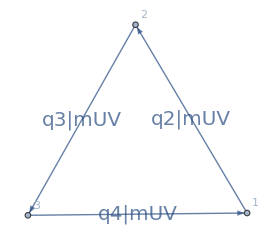

```mathematica
Tri1LUVTopology=DirectedGraph[{
DirectedEdge[1,2,2],
DirectedEdge[2,3,3],
DirectedEdge[3,1,4]
},VertexLabels->Automatic,EdgeLabels->Automatic];
Tri1LUVTopology=AssignSignatures[Tri1LUVTopology,masses-><|2->mUV,3->mUV,4->mUV|>,lmb->{3}];
Tri1LUVTopology=DirectedGraph[Tri1LUVTopology,VertexLabels->Automatic,ImageSize->275,GraphLayout->"HighDimensionalEmbedding",
EdgeLabels->Table[e->Style[("q"<>ToString[((e/.{DirectedEdge[_,_,props_]:>props})["id"])]<>"|"<>ToString[((e/.{DirectedEdge[_,_,props_]:>props})["mass"])]),FontSize->20],{e,EdgeList[Tri1LUVTopology]}]]
```

```mathematica
IRes=ComputeSubtractionTerm[SubtractionData["I"],Tri1Lnumerics];
```

```mathematica
SubtractionContribs=<||>;
```

### Numerator decomposition

```mathematica
Tri1L4DExpr=Num[Tri1Lnumerator]/Times@@Table[1/λ^2 Denom[ie,SP4[q[ie][λ],q[ie][λ]]-λ^2 m[ie]^2+(m[ie]^2-mUV^2)],{ie,GetVirtualPropagatorsIDs[Tri1L]}]
```

(λ^6 Num[-SP4[q[2],q[4]] SP4[q[3],q[6]]])/(Denom[2,-mUV^2+m[2]^2-λ^2 m[2]^2+SP4[q[2][λ],q[2][λ]]] Denom[3,-mUV^2+m[3]^2-λ^2 m[3]^2+SP4[q[3][λ],q[3][λ]]] Denom[4,-mUV^2+m[4]^2-λ^2 m[4]^2+SP4[q[4][λ],q[4][λ]]])

```mathematica
Tri1L4DExprWithFullLambdaDep=Collect[(1/λ)^4 Tri1L4DExpr/.
{
Num[x__]:>(x
/.
Table[q[ie]->1/λ q[ie][λ],{ie,GetVirtualPropagatorsIDs[Tri1L]}]
/.{
SP4[1/λ a_,1/λ b_]:>1/λ^2 SP4[a,b]
}/.
{SP4[1/λ a_,b_]:>1/λ SP4[a,b]}
)
},λ]
```

-(SP4[q[6],q[3][λ]] SP4[q[2][λ],q[4][λ]])/(λ Denom[2,-mUV^2+m[2]^2-λ^2 m[2]^2+SP4[q[2][λ],q[2][λ]]] Denom[3,-mUV^2+m[3]^2-λ^2 m[3]^2+SP4[q[3][λ],q[3][λ]]] Denom[4,-mUV^2+m[4]^2-λ^2 m[4]^2+SP4[q[4][λ],q[4][λ]]])

```mathematica
Tri1L4DExprWithFullLambdaDepDODsplits=Association[Table[pwr->λ^pwr Coefficient[Tri1L4DExprWithFullLambdaDep,λ^pwr],{pwr,{-1,1,2}}]]
```

<|-1→-(SP4[q[6],q[3][λ]] SP4[q[2][λ],q[4][λ]])/(λ Denom[2,-mUV^2+m[2]^2-λ^2 m[2]^2+SP4[q[2][λ],q[2][λ]]] Denom[3,-mUV^2+m[3]^2-λ^2 m[3]^2+SP4[q[3][λ],q[3][λ]]] Denom[4,-mUV^2+m[4]^2-λ^2 m[4]^2+SP4[q[4][λ],q[4][λ]]]),1→0,2→0|>

```mathematica
AssociateTo[Tri1L4DExprWithFullLambdaDepDODsplits,0->Tri1L4DExprWithFullLambdaDep-Total[Values[Tri1L4DExprWithFullLambdaDepDODsplits]]];
```

```mathematica
Tri1L4DExprWithFullLambdaDepDODsplits
```

<|-1→-(SP4[q[6],q[3][λ]] SP4[q[2][λ],q[4][λ]])/(λ Denom[2,-mUV^2+m[2]^2-λ^2 m[2]^2+SP4[q[2][λ],q[2][λ]]] Denom[3,-mUV^2+m[3]^2-λ^2 m[3]^2+SP4[q[3][λ],q[3][λ]]] Denom[4,-mUV^2+m[4]^2-λ^2 m[4]^2+SP4[q[4][λ],q[4][λ]]]),1→0,2→0,0→0|>

### Subtraction of λ^-1 leading UV contribution

```mathematica
Tri1L4DExprWithFullLambdaDepDODsplits[-1]
```

-(SP4[q[6],q[3][λ]] SP4[q[2][λ],q[4][λ]])/(λ Denom[2,-mUV^2+m[2]^2-λ^2 m[2]^2+SP4[q[2][λ],q[2][λ]]] Denom[3,-mUV^2+m[3]^2-λ^2 m[3]^2+SP4[q[3][λ],q[3][λ]]] Denom[4,-mUV^2+m[4]^2-λ^2 m[4]^2+SP4[q[4][λ],q[4][λ]]])

```mathematica
lm1Numerator=SeriesCoefficient[Series[Tri1L4DExprWithFullLambdaDepDODsplits[-1],{λ,0,0}],-1]/.{Denom[___]:>1}/.{q[a_][0]:>q[a]}(*/.{q[4]->p[1],q[5]->p[2],q[6]->(-p[1]-p[2])}*)
```

-SP4[q[2],q[4]] SP4[q[3],q[6]]

```mathematica
AssociateTo[SubtractionContribs,
"λm1CT"->{
<|
"cFFexpr"->ConvertCFFFormat[
CrossFreeFamilyLTD[Tri1LUVTopology,ConvertToNormalisedFormat->True],
Tri1LUVTopology],
"num"->lm1Numerator,
"graph"->Tri1LUVTopology,
"dots"-><|2->1,3->1,4->1|>
|>
}
];
```

```mathematica
SubtractionRes=Association[Table[k->Table[
(ComputeSubtractionTerm[
<|
"num"->(s["num"]/.UVExternalsDefinition),
"cFFexpr"->s["cFFexpr"],
"graph"->s["graph"]
|>,subtractionNumerics])
,{s,SubtractionContribs[k]}],{k,Keys[SubtractionContribs]}]];
```

```mathematica
AnalyzeSubtraction[IRes,SubtractionRes,-1]//MatrixForm
```

(orientation | I | -SumCT | I-SumCT | λm1CT#1
{-1,-1,1} | -0.214368 | 0.214368 | 0 | -0.214368
{-1,1,-1} | 0 | 0 | 0 | 0.
{-1,1,1} | -0.0457567 | 0.0457567 | 0 | -0.0457567
{1,-1,-1} | -0.214368 | 0.214368 | 0 | -0.214368
{1,-1,1} | 0 | 0 | 0 | 0.
{1,1,-1} | -0.0457567 | 0.0457567 | 0 | -0.0457567
TOTAL | -0.52025 | 0.52025 | 0 | -0.52025)

### Subtraction of λ^0 sub-leading UV contribution

```mathematica
Tri1L4DExprWithFullLambdaDepDODsplits[-1]
```

-(SP4[q[6],q[3][λ]] SP4[q[2][λ],q[4][λ]])/(λ Denom[2,-mUV^2+m[2]^2-λ^2 m[2]^2+SP4[q[2][λ],q[2][λ]]] Denom[3,-mUV^2+m[3]^2-λ^2 m[3]^2+SP4[q[3][λ],q[3][λ]]] Denom[4,-mUV^2+m[4]^2-λ^2 m[4]^2+SP4[q[4][λ],q[4][λ]]])

```mathematica
dod0Expr=SeriesCoefficient[Series[Tri1L4DExprWithFullLambdaDepDODsplits[-1]+Tri1L4DExprWithFullLambdaDepDODsplits[0],{λ,0,0}],0]//Expand;
```

```mathematica
dod0Expr
```

-(SP4[q[2][0],q[4][0]] q[3]'[0] SP4^(0,1)[q[6],q[3][0]])/(Denom[2,-mUV^2+m[2]^2+SP4[q[2][0],q[2][0]]] Denom[3,-mUV^2+m[3]^2+SP4[q[3][0],q[3][0]]] Denom[4,-mUV^2+m[4]^2+SP4[q[4][0],q[4][0]]])+(SP4[q[6],q[3][0]] SP4[q[2][0],q[4][0]] q[2]'[0] Denom^(0,1)[2,-mUV^2+m[2]^2+SP4[q[2][0],q[2][0]]] SP4^(0,1)[q[2][0],q[2][0]])/(Denom[2,-mUV^2+m[2]^2+SP4[q[2][0],q[2][0]]]^2 Denom[3,-mUV^2+m[3]^2+SP4[q[3][0],q[3][0]]] Denom[4,-mUV^2+m[4]^2+SP4[q[4][0],q[4][0]]])-(SP4[q[6],q[3][0]] q[4]'[0] SP4^(0,1)[q[2][0],q[4][0]])/(Denom[2,-mUV^2+m[2]^2+SP4[q[2][0],q[2][0]]] Denom[3,-mUV^2+m[3]^2+SP4[q[3][0],q[3][0]]] Denom[4,-mUV^2+m[4]^2+SP4[q[4][0],q[4][0]]])+(SP4[q[6],q[3][0]] SP4[q[2][0],q[4][0]] q[3]'[0] Denom^(0,1)[3,-mUV^2+m[3]^2+SP4[q[3][0],q[3][0]]] SP4^(0,1)[q[3][0],q[3][0]])/(Denom[2,-mUV^2+m[2]^2+SP4[q[2][0],q[2][0]]] Denom[3,-mUV^2+m[3]^2+SP4[q[3][0],q[3][0]]]^2 Denom[4,-mUV^2+m[4]^2+SP4[q[4][0],q[4][0]]])+(SP4[q[6],q[3][0]] SP4[q[2][0],q[4][0]] q[4]'[0] Denom^(0,1)[4,-mUV^2+m[4]^2+SP4[q[4][0],q[4][0]]] SP4^(0,1)[q[4][0],q[4][0]])/(Denom[2,-mUV^2+m[2]^2+SP4[q[2][0],q[2][0]]] Denom[3,-mUV^2+m[3]^2+SP4[q[3][0],q[3][0]]] Denom[4,-mUV^2+m[4]^2+SP4[q[4][0],q[4][0]]]^2)+(SP4[q[6],q[3][0]] SP4[q[2][0],q[4][0]] q[2]'[0] Denom^(0,1)[2,-mUV^2+m[2]^2+SP4[q[2][0],q[2][0]]] SP4^(1,0)[q[2][0],q[2][0]])/(Denom[2,-mUV^2+m[2]^2+SP4[q[2][0],q[2][0]]]^2 Denom[3,-mUV^2+m[3]^2+SP4[q[3][0],q[3][0]]] Denom[4,-mUV^2+m[4]^2+SP4[q[4][0],q[4][0]]])-(SP4[q[6],q[3][0]] q[2]'[0] SP4^(1,0)[q[2][0],q[4][0]])/(Denom[2,-mUV^2+m[2]^2+SP4[q[2][0],q[2][0]]] Denom[3,-mUV^2+m[3]^2+SP4[q[3][0],q[3][0]]] Denom[4,-mUV^2+m[4]^2+SP4[q[4][0],q[4][0]]])+(SP4[q[6],q[3][0]] SP4[q[2][0],q[4][0]] q[3]'[0] Denom^(0,1)[3,-mUV^2+m[3]^2+SP4[q[3][0],q[3][0]]] SP4^(1,0)[q[3][0],q[3][0]])/(Denom[2,-mUV^2+m[2]^2+SP4[q[2][0],q[2][0]]] Denom[3,-mUV^2+m[3]^2+SP4[q[3][0],q[3][0]]]^2 Denom[4,-mUV^2+m[4]^2+SP4[q[4][0],q[4][0]]])+(SP4[q[6],q[3][0]] SP4[q[2][0],q[4][0]] q[4]'[0] Denom^(0,1)[4,-mUV^2+m[4]^2+SP4[q[4][0],q[4][0]]] SP4^(1,0)[q[4][0],q[4][0]])/(Denom[2,-mUV^2+m[2]^2+SP4[q[2][0],q[2][0]]] Denom[3,-mUV^2+m[3]^2+SP4[q[3][0],q[3][0]]] Denom[4,-mUV^2+m[4]^2+SP4[q[4][0],q[4][0]]]^2)

Now split the above expression into its various denominator structures

```mathematica
Dataset[lmbDataLambda]
```

```mathematica
Tri1Lnumerator
```

-SP4[q[2],q[4]] SP4[q[3],q[6]]

```mathematica
dod0NumNoDot=<|
{}->ExpandSP4[(dod0Expr/.{x__*Denom[id_,y__]^-2:>0}/.{Denom[y__]:>1})/.{
x__*Derivative[1][q[ie_]][0]Derivative[0,1][SP4][a_,b_]:>x SP4[a,D[lmbDataLambda[ie]["lmb_decomposition"],λ]],
x__*Derivative[1][q[ie_]][0]Derivative[1,0][SP4][a_,b_]:>x SP4[D[lmbDataLambda[ie]["lmb_decomposition"],λ],b]
}/.SP4[0,x__]:>0
/.{q[ie_][0]->q[ie]}]
|>
```

<|{}→SP4[q[1],q[4]] SP4[q[3],q[6]]-SP4[q[2],q[6]] SP4[q[3],q[6]]|>

```mathematica
AssociateTo[SubtractionContribs,
"λ0CTDNumNoDot"->{
<|
"cFFexpr"->ConvertCFFFormat[
CrossFreeFamilyLTD[Tri1LUVTopology,ConvertToNormalisedFormat->True],
Tri1LUVTopology],
"num"->dod0NumNoDot[{}],
"graph"->Tri1LUVTopology,
"dots"-><|2->1,3->1,4->1|>
|>
}
];
```

```mathematica
dod0NumDotted=Association[Table[{{dot}->ExpandSP4[dod0Expr/.{x__/(Denom[idA_,__] Denom[idB_,__] Denom[idC_,__]):>0}/.{x__/(Denom[idA_,__] Denom[idB_,__] Denom[idC_?(!#1===dot&),__]^2):>0}/.{Denom[y__]:>1}/.x__ q[dot]'[0] Derivative[0,1][SP4][q[dot][0],q[dot][0]] Derivative[0,1][Denom][dot,z___]:>x SP4[q[dot],D[lmbDataLambda[dot]["lmb_decomposition"], λ]]/.x__ q[dot]'[0] Derivative[1,0][SP4][q[dot][0],q[dot][0]] Derivative[0,1][Denom][dot,z___]:>x SP4[q[dot],D[lmbDataLambda[dot]["lmb_decomposition"], λ]]/.SP4[0,x__]:>0/.{q[ie_][0]->q[ie]}]},{dot,
Sort[Table[(e/.{DirectedEdge[_,_,props_]:>props})["id"],{e,GetVirtualPropagators[Tri1L]}]]
}]]
```

<|{2}→-2 SP4[q[1],q[2]] SP4[q[2],q[4]] SP4[q[3],q[6]],{3}→0,{4}→2 SP4[q[2],q[4]] SP4[q[3],q[6]] SP4[q[4],q[6]]|>

```mathematica
AssociateTo[SubtractionContribs,
"λ0CTDDenomDotted"->
Table[
<|
"cFFexpr"->ConvertCFFFormat[
CrossFreeFamilyLTD[Tri1LUVTopology,ConvertToNormalisedFormat->True],
Tri1LUVTopology],
"num"->dod0NumDotted[d],
"graph"->Tri1LUVTopology,
"dots"-><|d⟦1⟧->2|>
|>
,{d,Sort[Keys[dod0NumDotted]]}]
];
```

```mathematica
(*
ComputeSubtractionTerm[
<|
"num"->(SubtractionContribs["λ0CTDDenomDotted"]⟦3⟧["num"]/.UVExternalsDefinition),
"cFFexpr"->SubtractionContribs["λ0CTDDenomDotted"]⟦3⟧["cFFexpr"],
"graph"->SubtractionContribs["λ0CTDDenomDotted"]⟦3⟧["graph"],
"dots"->SubtractionContribs["λ0CTDDenomDotted"]⟦3⟧["dots"]
|>,subtractionNumerics,
DebugNumerator->True,
NumeratorFudge->((Coefficient[#,(p[3][0])^2](p[3][0])^2)&)
][{-1,-1,1}]
*)
```

```mathematica
SubtractionRes=Association[Table[k->Table[
(ComputeSubtractionTerm[
<|
"num"->(s["num"]/.UVExternalsDefinition),
"cFFexpr"->s["cFFexpr"],
"graph"->s["graph"],
"dots"->s["dots"]
|>,subtractionNumerics
(*,NumeratorFudge->((Coefficient[#,(p[3][0])^2](p[3][0])^2)&)*)
])
,{s,SubtractionContribs[k]}],{k,Keys[SubtractionContribs]}]];
```

```mathematica
AnalyzeSubtraction[IRes,SubtractionRes,0,ExpansionDepth->0]//MatrixForm
```

(orientation | I | -SumCT | I-SumCT | λm1CT#1 | λ0CTDNumNoDot#1 | λ0CTDDenomDotted#1 | λ0CTDDenomDotted#2 | λ0CTDDenomDotted#3
{-1,-1,1} | -0.393498 | 0.393498 | 0 | 0. | 0.478426 | -0.270461 | 0. | -0.601463
{-1,1,-1} | 0 | 0 | 0 | 0. | 0.135555 | -0.0455826 | 0. | -0.0899725
{-1,1,1} | -0.11037 | 0.11037 | 0 | 0. | 0.102119 | -0.103312 | 0. | -0.109177
{1,-1,-1} | -0.535335 | 0.535335 | 0 | 0. | 0.303525 | -0.327369 | 0. | -0.511491
{1,-1,1} | 0 | 0 | 0 | 0. | 0.146881 | -0.0569082 | 0. | -0.0899725
{1,1,-1} | -0.192092 | 0.192092 | 0 | 0. | 0.0647871 | -0.0577296 | 0. | -0.19915
TOTAL | -1.23129 | 1.23129 | 0 | 0. | 1.23129 | -0.861363 | 0. | -1.60123)

Verify full cancellation indeed

```mathematica
Series[IRes[{-1,-1,1}]
-SubtractionRes["λm1CT"]⟦1⟧[{-1,-1,1}]
-SubtractionRes["λ0CTDNumNoDot"]⟦1⟧[{-1,-1,1}]
-SubtractionRes["λ0CTDDenomDotted"]⟦1⟧[{-1,-1,1}]
-SubtractionRes["λ0CTDDenomDotted"]⟦2⟧[{-1,-1,1}]
-SubtractionRes["λ0CTDDenomDotted"]⟦3⟧[{-1,-1,1}],{λ,0,1},Assumptions->{λ>0}]
```

-(121550625 (581941414760502089600234280397699732460383+10308895815938016803603309522763292240220 √14494) λ)/7789264547965739585797284148024518432149541891904+O[λ]^2

## Test Triangle-Box

### Input

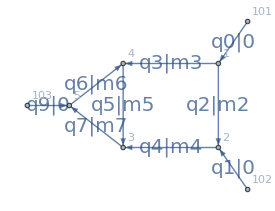

```mathematica
TriBox1L=DirectedGraph[{
DirectedEdge[101,1,0],
DirectedEdge[102,2,1],
DirectedEdge[1,2,2],
DirectedEdge[1,4,3],
DirectedEdge[2,3,4],
DirectedEdge[4,3,5],
DirectedEdge[5,4,6],
DirectedEdge[3,5,7],
DirectedEdge[103,5,9]
},VertexLabels->Automatic,EdgeLabels->Automatic];
TriBox1L=AssignSignatures[TriBox1L,masses-><|5->m5,6->m6,7->m7,3->m3,2->m2,4->m4|>,lmb->{7,4}];
TriBox1L=DirectedGraph[TriBox1L,VertexLabels->Automatic,ImageSize->275,GraphLayout->"HighDimensionalEmbedding",
EdgeLabels->Table[e->Style[("q"<>ToString[((e/.{DirectedEdge[_,_,props_]:>props})["id"])]<>"|"<>ToString[((e/.{DirectedEdge[_,_,props_]:>props})["mass"])]),FontSize->20],{e,EdgeList[TriBox1L]}]]
```

```mathematica
EdgeList[TriBox1L]
```

{1011<|id→0,sig→{{0,0},{1,0,0}},mass→0|>,1022<|id→1,sig→{{0,0},{0,1,0}},mass→0|>,12<|id→2,sig→{{0,1},{0,-1,0}},mass→m2|>,14<|id→3,sig→{{0,-1},{1,1,0}},mass→m3|>,23<|id→4,sig→{{0,1},{0,0,0}},mass→m4|>,43<|id→5,sig→{{1,-1},{0,0,0}},mass→m5|>,54<|id→6,sig→{{1,0},{-1,-1,0}},mass→m6|>,35<|id→7,sig→{{1,0},{0,0,0}},mass→m7|>,1035<|id→9,sig→{{0,0},{0,0,1}},mass→0|>}

```mathematica
lmbVec=q[cFFGetLMBEdges[TriBox1L]⟦1⟧/.{DirectedEdge[_,_,props_]:>props["id"]}]
```

q[7]

```mathematica
Dataset[GenerateLMBData[TriBox1L,loopshift->{q[0]:>(-q[1]-q[9])}]]
```

```mathematica
lmbData=GenerateLMBData[TriBox1L,loopshift->{q[0]:>(-q[1]-q[9])}];
lmbDataLambda=Association[Table[k-><|
"mass"->λ lmbData[k]["mass"],"lmb_decomposition"->Simplify[λ (lmbData[k]["lmb_decomposition"]/.{lmbVec->1/λ lmbVec})]|>,
{k,Keys[lmbData]}]]
```

<|0→<|mass→0,lmb_decomposition→λ q[0]|>,1→<|mass→0,lmb_decomposition→λ q[1]|>,2→<|mass→m2 λ,lmb_decomposition→λ (-q[1]+q[4])|>,3→<|mass→m3 λ,lmb_decomposition→-λ (q[4]+q[9])|>,4→<|mass→m4 λ,lmb_decomposition→λ q[4]|>,5→<|mass→m5 λ,lmb_decomposition→-λ q[4]+q[7]|>,6→<|mass→m6 λ,lmb_decomposition→q[7]+λ q[9]|>,7→<|mass→m7 λ,lmb_decomposition→q[7]|>,9→<|mass→0,lmb_decomposition→λ q[9]|>|>

```mathematica
TriBox1Lnumerics=Join[GenerateRandomSample[TriBox1L,Seed->1],{m2->2,m3->3,m4->4,m5->5,m6->6,m7->7}]
```

{k1→{2/3,3/5,5/7},k2→{7/11,11/13,13/17},p1→{17/19,19/23,23/29},p2→{29/31,31/37,37/41},p1E→41/43,p2E→43/47,p3→{-1078/589,-1416/851,-2016/1189},p3E→-3776/2021,m2→2,m3→3,m4→4,m5→5,m6→6,m7→7}

```mathematica
TriBox1LParameters = {
k1->{k1x,k1y,k1z},
k2->{k2x,k2y,k2z},
p1->{p1x,p1y,p1z},
p2->{p2x,p2y,p2z},
p3->{p3x,p3y,p3z},
p1E->p1E,
p2E->p2E,
p3E->p3E
};
```

See how some small off-shellness in the external violates the subtraction

```mathematica
(* TriBox1Lnumerics=Join[TriBox1Lnumerics⟦;;-2⟧,{p3E->Evaluate[(p3E/.Tri1Lnumerics)]+1/3}] *)
```

```mathematica
subtractionNumerics=Join[
TriBox1Lnumerics,
{mUV->10,
p[1][0]->(p1E/.TriBox1Lnumerics),p[2][0]->(p2E/.TriBox1Lnumerics),p[3][0]->(p3E/.TriBox1Lnumerics),
p[1]->(p1/.TriBox1Lnumerics),p[2]->(p2/.TriBox1Lnumerics),p[3]->(p3/.TriBox1Lnumerics)
}];
```

```mathematica
UVExternalsDefinition=Block[
{
externalEdges,externalEdgesIDs,momLabels,signatures
},
externalEdges=cFFGetExternalEdges[TriBox1L];
externalEdgesIDs=Table[Evaluate[(ee/.{DirectedEdge[_,_,props_]:>props})]["id"],{ee,externalEdges}];
momLabels=cFFGenerateMomentaLabels[TriBox1L];
signatures=Association[Table[((#["id"]->#["sig"])&)[e/.{DirectedEdge[_,_,props_]:>props}],{e,EdgeList[TriBox1L]}]];

Join[
(*Table[
q[eeID]->(signatures[eeID][[1]] . momLabels[[1]]+signatures[eeID][[2]] . momLabels[[2]])
,{eeID,externalEdgesIDs}],*)
Table[
q[externalEdgesIDs⟦ieeID⟧]->p[ieeID]
,{ieeID,Length[externalEdgesIDs]}],
Table[
qE[externalEdgesIDs⟦ieeID⟧]->ToExpression["p"<>ToString[ieeID]<>"E"]
,{ieeID,Length[externalEdgesIDs]}]
]
]
```

{q[0]→p[1],q[1]→p[2],q[9]→p[3],qE[0]→p1E,qE[1]→p2E,qE[9]→p3E}

```mathematica
TriBox1Lnumerator=SP4[q[5],q[6]]SP4[q[7],q[9]];
```

```mathematica
SubtractionData=<|
"I"-><|
"cFFexpr"->ConvertCFFFormat[CrossFreeFamilyLTD[TriBox1L,ConvertToNormalisedFormat->True],TriBox1L],
"num"->TriBox1Lnumerator,
"graph"->TriBox1L
|>
|>;
```

```mathematica
ComputeOSEReplacements[TriBox1L,TriBox1Lnumerics/.{Rule[k1,a_]->Rule[k1,1/λ a]}]
```

{OSE[0]:>(3 √37688387)/12673,OSE[1]:>(3 √587654619)/47027,OSE[2]:>(2 √13424220810010598)/114322637,OSE[3]:>(2 √6276430292742294894619305)/1448810778701,OSE[4]:>(√104636515)/2431,OSE[5]:>√(25+(-11/13+3/(5 λ))^2+(-7/11+2/(3 λ))^2+(-13/17+5/(7 λ))^2),OSE[6]:>√(36+(-1416/851+3/(5 λ))^2+(-1078/589+2/(3 λ))^2+(-2016/1189+5/(7 λ))^2),OSE[7]:>√(49+14494/(11025 λ^2)),OSE[9]:>(2 √798561818988978409)/595973171}

```mathematica
EdgeList[GraphDifference[TriBox1L,DirectedGraph[cFFGetExternalEdges[TriBox1L]]]]
```

{12<|id→2,sig→{{0,1},{0,-1,0}},mass→m2|>,14<|id→3,sig→{{0,-1},{1,1,0}},mass→m3|>,23<|id→4,sig→{{0,1},{0,0,0}},mass→m4|>,35<|id→7,sig→{{1,0},{0,0,0}},mass→m7|>,43<|id→5,sig→{{1,-1},{0,0,0}},mass→m5|>,54<|id→6,sig→{{1,0},{-1,-1,0}},mass→m6|>}

```mathematica
EdgeList[GraphDifference[TriBox1LUVTopology,DirectedGraph[cFFGetExternalEdges[TriBox1LUVTopology]]]]
```

{12<|id→2,sig→{{0,1},{}},mass→m2|>,14<|id→3,sig→{{0,-1},{}},mass→m3|>,23<|id→4,sig→{{0,1},{}},mass→m4|>,35<|id→7,sig→{{1,0},{}},mass→mUV|>,43<|id→5,sig→{{1,-1},{}},mass→mUV|>,54<|id→6,sig→{{1,0},{}},mass→mUV|>}

Test the new evaluation model against the old one

```mathematica
Simplify[
ComputeSubtractionTermFromNormalized[
<|
"cFFexpr"->CrossFreeFamilyLTD[TriBox1L,ConvertToNormalisedFormat->True],
"num"->TriBox1Lnumerator,
"graph"->TriBox1L
|>,
TriBox1Lnumerics][{-1,-1,-1,-1,-1,1}]
-
ComputeSubtractionTerm[
<|
"cFFexpr"->ConvertCFFFormat[CrossFreeFamilyLTD[TriBox1L,ConvertToNormalisedFormat->True],TriBox1L],
"num"->TriBox1Lnumerator,
"graph"->TriBox1L,
"dots"-><|2->1|>
|>,
TriBox1Lnumerics(*{}*)][{-1,-1,-1,-1,-1,1}]
]
```

0

```mathematica
ComputeSubtractionTerm[
<|
"cFFexpr"->ConvertCFFFormat[CrossFreeFamilyLTD[TriBox1L,ConvertToNormalisedFormat->True],TriBox1L],
"num"->TriBox1Lnumerator,
"graph"->TriBox1L,
"dots"-><|2->1|>
|>,
{}][{-1,-1,-1,-1,-1,1}]
```

((-(k1-k2).(k1-p1-p2)+OSE[5] OSE[6]) (-k1.p3+p3E OSE[7]) (1/((p1E+OSE[2]+OSE[3]) (p1E+p2E+OSE[3]+OSE[4]) (OSE[4]+OSE[5]+OSE[7]) (-p1E-p2E+OSE[6]+OSE[7]))+1/((p1E+OSE[2]+OSE[3]) (-p2E+OSE[2]+OSE[5]+OSE[7]) (OSE[4]+OSE[5]+OSE[7]) (-p1E-p2E+OSE[6]+OSE[7]))))/(64 λ^3 OSE[2] OSE[3] OSE[4] OSE[5] OSE[6] OSE[7])

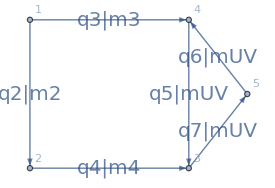

```mathematica
TriBox1LUVTopology=DirectedGraph[{
DirectedEdge[1,2,2],
DirectedEdge[1,4,3],
DirectedEdge[2,3,4],
DirectedEdge[4,3,5],
DirectedEdge[5,4,6],
DirectedEdge[3,5,7]
},VertexLabels->Automatic,EdgeLabels->Automatic];
TriBox1LUVTopology=AssignSignatures[TriBox1LUVTopology,masses-><|5->mUV,6->mUV,7->mUV,3->m3,2->m2,4->m4|>,lmb->{7,4}];
(* Force the loop momentum routing to be identical as in the original graph *)
(* Just to be safe *)
TriBox1LUVTopology = Block[{signatures,tmp},
signatures=Association[Table[((#["id"]->#["sig"])&)[e/.{DirectedEdge[_,_,props_]:>props}],{e,EdgeList[TriBox1L]}]];
DirectedGraph[Table[
tmp=e/.{DirectedEdge[a_,b_,props_]:>props};
e/.{DirectedEdge[a_,b_,props_]:> DirectedEdge[a,b,Association[Table[k->If[k==="sig",
{signatures[tmp["id"]]⟦1⟧,tmp[k]⟦2⟧}
,tmp[k]],{k,Keys[tmp]}]]]}
,{e,EdgeList[TriBox1LUVTopology]}]]
];
TriBox1LUVTopology=DirectedGraph[TriBox1LUVTopology,VertexLabels->Automatic,ImageSize->275,GraphLayout->"HighDimensionalEmbedding",
EdgeLabels->Table[e->Style[("q"<>ToString[((e/.{DirectedEdge[_,_,props_]:>props})["id"])]<>"|"<>ToString[((e/.{DirectedEdge[_,_,props_]:>props})["mass"])]),FontSize->20],{e,EdgeList[TriBox1LUVTopology]}]]
```

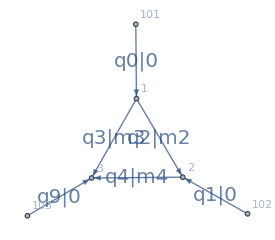

```mathematica
TriBox1LUVTopologyFactor=DirectedGraph[{
DirectedEdge[101,1,0],
DirectedEdge[102,2,1],
DirectedEdge[1,2,2],
DirectedEdge[1,3,3],
DirectedEdge[2,3,4],
DirectedEdge[103,3,9]
},VertexLabels->Automatic,EdgeLabels->Automatic];
TriBox1LUVTopologyFactor=AssignSignatures[TriBox1LUVTopologyFactor,masses-><|5->mUV,6->mUV,7->mUV,3->m3,2->m2,4->m4|>,lmb->{7,4}];
(* Force the loop momentum routing to be identical as in the original graph *)
(* Just to be safe *)
TriBox1LUVTopologyFactor = Block[{signatures,tmp},
signatures=Association[Table[((#["id"]->#["sig"])&)[e/.{DirectedEdge[_,_,props_]:>props}],{e,EdgeList[TriBox1L]}]];
DirectedGraph[Table[
tmp=e/.{DirectedEdge[a_,b_,props_]:>props};
e/.{DirectedEdge[a_,b_,props_]:> DirectedEdge[a,b,Association[Table[k->If[k==="sig",
{signatures[tmp["id"]]⟦1⟧,signatures[tmp["id"]]⟦2⟧(*,tmp[k]⟦2⟧*)}
,tmp[k]],{k,Keys[tmp]}]]]}
,{e,EdgeList[TriBox1LUVTopologyFactor]}]]
];
TriBox1LUVTopologyFactor=DirectedGraph[TriBox1LUVTopologyFactor,VertexLabels->Automatic,ImageSize->275,GraphLayout->"HighDimensionalEmbedding",
EdgeLabels->Table[e->Style[("q"<>ToString[((e/.{DirectedEdge[_,_,props_]:>props})["id"])]<>"|"<>ToString[((e/.{DirectedEdge[_,_,props_]:>props})["mass"])]),FontSize->20],{e,EdgeList[TriBox1LUVTopologyFactor]}]]
```

```mathematica
EdgeList[TriBox1LUVTopologyFactor]
```

{1011<|id→0,sig→{{0,0},{1,0,0}},mass→0|>,1022<|id→1,sig→{{0,0},{0,1,0}},mass→0|>,12<|id→2,sig→{{0,1},{0,-1,0}},mass→m2|>,13<|id→3,sig→{{0,-1},{1,1,0}},mass→m3|>,23<|id→4,sig→{{0,1},{0,0,0}},mass→m4|>,1033<|id→9,sig→{{0,0},{0,0,1}},mass→0|>}

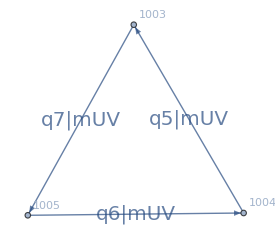

```mathematica
TriBox1LUVTopologyVac=DirectedGraph[{
DirectedEdge[1004,1003,5],
DirectedEdge[1005,1004,6],
DirectedEdge[1003,1005,7]
},VertexLabels->Automatic,EdgeLabels->Automatic];
TriBox1LUVTopologyVac=AssignSignatures[TriBox1LUVTopologyVac,masses-><|5->mUV,6->mUV,7->mUV,3->1,2->1,4->1|>,lmb->{7,4}];
(* Force the loop momentum routing to be identical as in the original graph *)
(* Just to be safe *)
TriBox1LUVTopologyVac = Block[{signatures,tmp},
(*signatures=Association[Table[((#["id"]->#["sig"])&)[e/.{DirectedEdge[_,_,props_]:>props}],{e,EdgeList[TriBox1L]}]];*)
signatures=Association[Table[((#["id"]->{{1,0},{0,0,0}})&)[e/.{DirectedEdge[_,_,props_]:>props}],{e,EdgeList[TriBox1LUVTopologyVac]}]];
DirectedGraph[Table[
tmp=e/.{DirectedEdge[a_,b_,props_]:>props};
e/.{DirectedEdge[a_,b_,props_]:> DirectedEdge[a,b,Association[Table[k->If[k==="sig",
{signatures[tmp["id"]]⟦1⟧,signatures[tmp["id"]]⟦2⟧}
,tmp[k]],{k,Keys[tmp]}]]]}
,{e,EdgeList[TriBox1LUVTopologyVac]}]]
];
TriBox1LUVTopologyVac=DirectedGraph[TriBox1LUVTopologyVac,VertexLabels->Automatic,ImageSize->275,GraphLayout->"HighDimensionalEmbedding",
EdgeLabels->Table[e->Style[("q"<>ToString[((e/.{DirectedEdge[_,_,props_]:>props})["id"])]<>"|"<>ToString[((e/.{DirectedEdge[_,_,props_]:>props})["mass"])]),FontSize->20],{e,EdgeList[TriBox1LUVTopologyVac]}]]
```

```mathematica
EdgeList[TriBox1L]
```

{1011<|id→0,sig→{{0,0},{1,0,0}},mass→0|>,1022<|id→1,sig→{{0,0},{0,1,0}},mass→0|>,12<|id→2,sig→{{0,1},{0,-1,0}},mass→m2|>,14<|id→3,sig→{{0,-1},{1,1,0}},mass→m3|>,23<|id→4,sig→{{0,1},{0,0,0}},mass→m4|>,43<|id→5,sig→{{1,-1},{0,0,0}},mass→m5|>,54<|id→6,sig→{{1,0},{-1,-1,0}},mass→m6|>,35<|id→7,sig→{{1,0},{0,0,0}},mass→m7|>,1035<|id→9,sig→{{0,0},{0,0,1}},mass→0|>}

```mathematica
EdgeList[TriBox1LUVTopologyVac]
```

{10041003<|id→5,sig→{{1,0},{0,0,0}},mass→mUV|>,10051004<|id→6,sig→{{1,0},{0,0,0}},mass→mUV|>,10031005<|id→7,sig→{{1,0},{0,0,0}},mass→mUV|>}

```mathematica
TriBox1L
```

-Graphics-

```mathematica
List@@@Normal[<|1->2,4->3|>]
```

{{1,2},{4,3}}

```mathematica
Association[{1->2,3->4}]
```

<|1→2,3→4|>

```mathematica
CombineGraphs[gs_]:=DirectedGraph[Join@@Table[EdgeList[g],{g, gs}]]
```

```mathematica
MergeCFFExpr[exprs_]:=Block[
{combinedExpr,newO,O},
combinedExpr=exprs[[1]];
Do[
combinedExpr=Flatten[
Table[Table[
{Association[Table[co⟦1⟧->co[[2]],{co,SortBy[Join[List@@@Normal[o⟦1⟧],List@@@Normal[newO⟦1⟧]],(#⟦1⟧)&]}]],o⟦2⟧*newO⟦2⟧}
,{newO,e}],
{o,combinedExpr}],
1
];
,{e,exprs⟦2;;⟧}];
combinedExpr
]
```

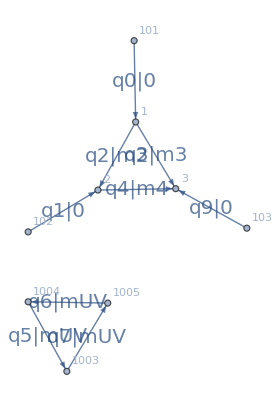

```mathematica
DirectedGraph[EdgeList[CombineGraphs[{TriBox1LUVTopologyFactor,TriBox1LUVTopologyVac}]],VertexLabels->Automatic,ImageSize->275,
EdgeLabels->Table[e->Style[("q"<>ToString[((e/.{DirectedEdge[_,_,props_]:>props})["id"])]<>"|"<>ToString[((e/.{DirectedEdge[_,_,props_]:>props})["mass"])]),FontSize->20],{e,EdgeList[CombineGraphs[{TriBox1LUVTopologyFactor,TriBox1LUVTopologyVac}]]}]]
```

```mathematica
MergeCFFExpr[{
ConvertCFFFormat[
CrossFreeFamilyLTD[TriBox1LUVTopologyFactor,ConvertToNormalisedFormat->True],
TriBox1LUVTopologyFactor],
ConvertCFFFormat[
CrossFreeFamilyLTD[TriBox1LUVTopologyVac,ConvertToNormalisedFormat->True],
TriBox1LUVTopologyVac]
}]//Length
```

36

```mathematica
ConvertCFFFormat[
CrossFreeFamilyLTD[TriBox1LUVTopologyFactor,ConvertToNormalisedFormat->True],
TriBox1LUVTopologyFactor]//Length
```

6

```mathematica
ConvertCFFFormat[
CrossFreeFamilyLTD[TriBox1LUVTopologyVac,ConvertToNormalisedFormat->True],
TriBox1LUVTopologyVac]//Length
```

6

```mathematica
IRes=ComputeSubtractionTerm[SubtractionData["I"],TriBox1Lnumerics];
```

```mathematica
SubtractionContribs=<||>;
```

### Numerator decomposition

```mathematica
UVPropagatorsTriBox1L={5,6,7};
```

```mathematica
SymmetricDifference[GetVirtualPropagatorsIDs[TriBox1L],UVPropagatorsTriBox1L]
```

{2,3,4}

```mathematica
TriBox1L4DExpr=Num[TriBox1Lnumerator]/Times@@Table[1/λ^2 Denom[ie,SP4[q[ie][λ],q[ie][λ]]-λ^2 m[ie]^2+(m[ie]^2-mUV^2)],{ie,UVPropagatorsTriBox1L}]/Times@@Table[Denom[ie,SP4[q[ie],q[ie]]-m[ie]^2],{ie,SymmetricDifference[GetVirtualPropagatorsIDs[TriBox1L],UVPropagatorsTriBox1L]}]
```

(λ^6 Num[SP4[q[5],q[6]] SP4[q[7],q[9]]])/(Denom[2,-m[2]^2+SP4[q[2],q[2]]] Denom[3,-m[3]^2+SP4[q[3],q[3]]] Denom[4,-m[4]^2+SP4[q[4],q[4]]] Denom[5,-mUV^2+m[5]^2-λ^2 m[5]^2+SP4[q[5][λ],q[5][λ]]] Denom[6,-mUV^2+m[6]^2-λ^2 m[6]^2+SP4[q[6][λ],q[6][λ]]] Denom[7,-mUV^2+m[7]^2-λ^2 m[7]^2+SP4[q[7][λ],q[7][λ]]])

```mathematica
TriBox1L4DExprWithFullLambdaDep=Collect[(1/λ)^4 TriBox1L4DExpr/.
{
Num[x__]:>(x
/.
Table[q[ie]->1/λ q[ie][λ],{ie,GetVirtualPropagatorsIDs[TriBox1L]}]
/.{
SP4[1/λ a_,1/λ b_]:>1/λ^2 SP4[a,b]
}/.
{SP4[1/λ a_,b_]:>1/λ SP4[a,b]}
)
},λ]
```

(SP4[q[9],q[7][λ]] SP4[q[5][λ],q[6][λ]])/(λ Denom[2,-m[2]^2+SP4[q[2],q[2]]] Denom[3,-m[3]^2+SP4[q[3],q[3]]] Denom[4,-m[4]^2+SP4[q[4],q[4]]] Denom[5,-mUV^2+m[5]^2-λ^2 m[5]^2+SP4[q[5][λ],q[5][λ]]] Denom[6,-mUV^2+m[6]^2-λ^2 m[6]^2+SP4[q[6][λ],q[6][λ]]] Denom[7,-mUV^2+m[7]^2-λ^2 m[7]^2+SP4[q[7][λ],q[7][λ]]])

```mathematica
TriBox1L4DExprWithFullLambdaDepDODsplits=Association[Table[pwr->λ^pwr Coefficient[TriBox1L4DExprWithFullLambdaDep,λ^pwr],{pwr,{-1,1,2}}]]
```

<|-1→(SP4[q[9],q[7][λ]] SP4[q[5][λ],q[6][λ]])/(λ Denom[2,-m[2]^2+SP4[q[2],q[2]]] Denom[3,-m[3]^2+SP4[q[3],q[3]]] Denom[4,-m[4]^2+SP4[q[4],q[4]]] Denom[5,-mUV^2+m[5]^2-λ^2 m[5]^2+SP4[q[5][λ],q[5][λ]]] Denom[6,-mUV^2+m[6]^2-λ^2 m[6]^2+SP4[q[6][λ],q[6][λ]]] Denom[7,-mUV^2+m[7]^2-λ^2 m[7]^2+SP4[q[7][λ],q[7][λ]]]),1→0,2→0|>

```mathematica
AssociateTo[TriBox1L4DExprWithFullLambdaDepDODsplits,0->TriBox1L4DExprWithFullLambdaDep-Total[Values[TriBox1L4DExprWithFullLambdaDepDODsplits]]];
```

```mathematica
TriBox1L4DExprWithFullLambdaDepDODsplits
```

<|-1→(SP4[q[9],q[7][λ]] SP4[q[5][λ],q[6][λ]])/(λ Denom[2,-m[2]^2+SP4[q[2],q[2]]] Denom[3,-m[3]^2+SP4[q[3],q[3]]] Denom[4,-m[4]^2+SP4[q[4],q[4]]] Denom[5,-mUV^2+m[5]^2-λ^2 m[5]^2+SP4[q[5][λ],q[5][λ]]] Denom[6,-mUV^2+m[6]^2-λ^2 m[6]^2+SP4[q[6][λ],q[6][λ]]] Denom[7,-mUV^2+m[7]^2-λ^2 m[7]^2+SP4[q[7][λ],q[7][λ]]]),1→0,2→0,0→0|>

### Subtraction of λ^-1 leading UV contribution

```mathematica
TriBox1L4DExprWithFullLambdaDepDODsplits[-1]
```

(SP4[q[9],q[7][λ]] SP4[q[5][λ],q[6][λ]])/(λ Denom[2,-m[2]^2+SP4[q[2],q[2]]] Denom[3,-m[3]^2+SP4[q[3],q[3]]] Denom[4,-m[4]^2+SP4[q[4],q[4]]] Denom[5,-mUV^2+m[5]^2-λ^2 m[5]^2+SP4[q[5][λ],q[5][λ]]] Denom[6,-mUV^2+m[6]^2-λ^2 m[6]^2+SP4[q[6][λ],q[6][λ]]] Denom[7,-mUV^2+m[7]^2-λ^2 m[7]^2+SP4[q[7][λ],q[7][λ]]])

```mathematica
lm1Numerator=SeriesCoefficient[Series[TriBox1L4DExprWithFullLambdaDepDODsplits[-1],{λ,0,0}],-1]/.{Denom[___]:>1}/.{q[a_][0]:>q[a]}(*/.{q[4]->p[1],q[5]->p[2],q[6]->(-p[1]-p[2])}*)
```

SP4[q[5],q[6]] SP4[q[7],q[9]]

```mathematica
AssociateTo[SubtractionContribs,
"λm1CT"->{
<|
"cFFexpr"->MergeCFFExpr[{
ConvertCFFFormat[
CrossFreeFamilyLTD[TriBox1LUVTopologyFactor,ConvertToNormalisedFormat->True],
TriBox1LUVTopologyFactor],
ConvertCFFFormat[
CrossFreeFamilyLTD[TriBox1LUVTopologyVac,ConvertToNormalisedFormat->True],
TriBox1LUVTopologyVac]
}],
"num"->lm1Numerator,
"graph"->CombineGraphs[{TriBox1LUVTopologyVac,TriBox1LUVTopologyFactor}],
"dots"-><||>
|>
}
];
```

```mathematica
subtractionNumerics
```

{k1→{2/3,3/5,5/7},k2→{7/11,11/13,13/17},p1→{17/19,19/23,23/29},p2→{29/31,31/37,37/41},p1E→41/43,p2E→43/47,p3→{-1078/589,-1416/851,-2016/1189},p3E→-3776/2021,m2→2,m3→3,m4→4,m5→5,m6→6,m7→7,mUV→10,p[1][0]→41/43,p[2][0]→43/47,p[3][0]→-3776/2021,p[1]→{17/19,19/23,23/29},p[2]→{29/31,31/37,37/41},p[3]→{-1078/589,-1416/851,-2016/1189}}

```mathematica
UVExternalsDefinition
```

{q[0]→p[1],q[1]→p[2],q[9]→p[3],qE[0]→p1E,qE[1]→p2E,qE[9]→p3E}

```mathematica
SubtractionRes=Association[Table[k->Table[
(ComputeSubtractionTerm[
<|
"num"->(s["num"]/.UVExternalsDefinition),
"cFFexpr"->s["cFFexpr"],
"graph"->s["graph"]
|>,subtractionNumerics])
,{s,SubtractionContribs[k]}],{k,Keys[SubtractionContribs]}]];
```

```mathematica
SubtractionContribs["λm1CT"]⟦1⟧["cFFexpr"];
SubtractionRes["λm1CT"]⟦1⟧;
```

```mathematica
ComputeSubtractionTerm[SubtractionData["I"],{}][{-1,-1,-1,-1,1,-1}]
```

((-(k1-k2).(k1-p1-p2)-OSE[5] OSE[6]) (-k1.p3-p3E OSE[7]) (1/((p1E+OSE[2]+OSE[3]) (p1E+p2E+OSE[3]+OSE[4]) (p1E+p2E+OSE[4]+OSE[5]+OSE[6]) (p1E+p2E+OSE[6]+OSE[7]))+1/((p1E+OSE[2]+OSE[3]) (p1E+OSE[2]+OSE[5]+OSE[6]) (p1E+p2E+OSE[4]+OSE[5]+OSE[6]) (p1E+p2E+OSE[6]+OSE[7]))))/(64 λ^3 OSE[2] OSE[3] OSE[4] OSE[5] OSE[6] OSE[7])

```mathematica
ComputeSubtractionTerm[
<|
"num"->(SubtractionContribs["λm1CT"]⟦1⟧["num"]/.UVExternalsDefinition),
"cFFexpr"->SubtractionContribs["λm1CT"]⟦1⟧["cFFexpr"],
"graph"->SubtractionContribs["λm1CT"]⟦1⟧["graph"]
|>,{}][{-1,-1,-1,-1,1,-1}]
```

((-k1.k1-OSE[5] OSE[6]) (-p[3].k1-OSE[7] p[3][0]))/(64 λ^3 OSE[2] OSE[3] (p1E+OSE[2]+OSE[3]) OSE[4] (p1E+p2E+OSE[3]+OSE[4]) OSE[5] OSE[6] (OSE[5]+OSE[6]) OSE[7] (OSE[6]+OSE[7]))

```mathematica
subtractionNumerics
```

{k1→{2/3,3/5,5/7},k2→{7/11,11/13,13/17},p1→{17/19,19/23,23/29},p2→{29/31,31/37,37/41},p1E→41/43,p2E→43/47,p3→{-1078/589,-1416/851,-2016/1189},p3E→-3776/2021,m2→2,m3→3,m4→4,m5→5,m6→6,m7→7,mUV→10,p[1][0]→41/43,p[2][0]→43/47,p[3][0]→-3776/2021,p[1]→{17/19,19/23,23/29},p[2]→{29/31,31/37,37/41},p[3]→{-1078/589,-1416/851,-2016/1189}}

```mathematica
AnalyzeSubtraction[IRes,SubtractionRes,-1
(*,SelectedOrientations->{
{-1,-1,-1,-1,1,-1},
{-1,-1,-1,-1,1,1}
}
*)
]//MatrixForm
```

(orientation | I | -SumCT | I-SumCT | λm1CT#1
{-1,-1,-1,-1,-1,1} | 0 | 0 | 0 | 0.
{-1,-1,-1,-1,1,-1} | -0.0000159475 | 0.0000159475 | 0 | -0.0000159475
{-1,-1,-1,-1,1,1} | -3.6846×10^-6 | 3.6846×10^-6 | 0 | -3.6846×10^-6
{-1,-1,-1,1,-1,-1} | -0.0000159475 | 0.0000159475 | 0 | -0.0000159475
{-1,-1,-1,1,-1,1} | -3.6846×10^-6 | 3.6846×10^-6 | 0 | -3.6846×10^-6
{-1,-1,-1,1,1,-1} | 0 | 0 | 0 | 0.
{-1,-1,1,-1,-1,1} | 0 | 0 | 0 | 0.
{-1,-1,1,-1,1,-1} | -0.0000285821 | 0.0000285821 | 0 | -0.0000285821
{-1,-1,1,-1,1,1} | -6.60376×10^-6 | 6.60376×10^-6 | 0 | -6.60376×10^-6
{-1,-1,1,1,-1,-1} | -0.0000285821 | 0.0000285821 | 0 | -0.0000285821
{-1,-1,1,1,-1,1} | -6.60376×10^-6 | 6.60376×10^-6 | 0 | -6.60376×10^-6
{-1,-1,1,1,1,-1} | 0 | 0 | 0 | 0.
{-1,1,-1,-1,-1,1} | 0 | 0 | 0 | 0.
{-1,1,-1,-1,1,-1} | 0 | 0 | 0 | 0.
{-1,1,-1,-1,1,1} | 0 | 0 | 0 | 0.
{-1,1,1,-1,-1,1} | 0 | 0 | 0 | 0.
{-1,1,1,-1,1,-1} | -0.0000317421 | 0.0000317421 | 0 | -0.0000317421
{-1,1,1,-1,1,1} | -7.33387×10^-6 | 7.33387×10^-6 | 0 | -7.33387×10^-6
{-1,1,1,1,-1,-1} | -0.0000317421 | 0.0000317421 | 0 | -0.0000317421
{-1,1,1,1,-1,1} | -7.33387×10^-6 | 7.33387×10^-6 | 0 | -7.33387×10^-6
{-1,1,1,1,1,-1} | 0 | 0 | 0 | 0.
{1,-1,-1,-1,-1,1} | 0 | 0 | 0 | 0.
{1,-1,-1,-1,1,-1} | -0.000014362 | 0.000014362 | 0 | -0.000014362
{1,-1,-1,-1,1,1} | -3.31827×10^-6 | 3.31827×10^-6 | 0 | -3.31827×10^-6
{1,-1,-1,1,-1,-1} | -0.000014362 | 0.000014362 | 0 | -0.000014362
{1,-1,-1,1,-1,1} | -3.31827×10^-6 | 3.31827×10^-6 | 0 | -3.31827×10^-6
{1,-1,-1,1,1,-1} | 0 | 0 | 0 | 0.
{1,-1,1,1,-1,-1} | 0 | 0 | 0 | 0.
{1,-1,1,1,-1,1} | 0 | 0 | 0 | 0.
{1,-1,1,1,1,-1} | 0 | 0 | 0 | 0.
{1,1,-1,-1,-1,1} | 0 | 0 | 0 | 0.
{1,1,-1,-1,1,-1} | -0.0000302163 | 0.0000302163 | 0 | -0.0000302163
{1,1,-1,-1,1,1} | -6.98133×10^-6 | 6.98133×10^-6 | 0 | -6.98133×10^-6
{1,1,-1,1,-1,-1} | -0.0000302163 | 0.0000302163 | 0 | -0.0000302163
{1,1,-1,1,-1,1} | -6.98133×10^-6 | 6.98133×10^-6 | 0 | -6.98133×10^-6
{1,1,-1,1,1,-1} | 0 | 0 | 0 | 0.
{1,1,1,-1,-1,1} | 0 | 0 | 0 | 0.
{1,1,1,-1,1,-1} | -0.0000372615 | 0.0000372615 | 0 | -0.0000372615
{1,1,1,-1,1,1} | -8.6091×10^-6 | 8.6091×10^-6 | 0 | -8.6091×10^-6
{1,1,1,1,-1,-1} | -0.0000372615 | 0.0000372615 | 0 | -0.0000372615
{1,1,1,1,-1,1} | -8.6091×10^-6 | 8.6091×10^-6 | 0 | -8.6091×10^-6
{1,1,1,1,1,-1} | 0 | 0 | 0 | 0.
TOTAL | -0.000389285 | 0.000389285 | 0 | -0.000389285)

```mathematica
MatrixForm[Table[MatrixForm[N[SubtractionRes["λm1CT"]⟦1⟧[o]/.{λ->1},40]],{o,Keys[SubtractionRes["λm1CT"]⟦1⟧]}]]
Total[Table[N[SubtractionRes["λm1CT"]⟦1⟧[o]/.{λ->1},40],{o,Keys[SubtractionRes["λm1CT"]⟦1⟧]}]]
```

(-3.210389457092423067626831719926118493675×10^-8
-4.764544828932335898429852414574640869049×10^-8
3.29480013245042321264666536881248431943×10^-8
-4.764544828932335898429852414574640869049×10^-8
3.29480013245042321264666536881248431943×10^-8
4.642480233018733144336406826292935990595×10^-8
-5.753856123238331770084941644919461331297×10^-8
-8.539308331527025007044409107212167628009×10^-8
5.905142092671830873351356418981071621611×10^-8
-8.539308331527025007044409107212167628009×10^-8
5.905142092671830873351356418981071621611×10^-8
8.320536705213440239990579697443909975077×10^-8
-6.389996117731871931742013492315012732109×10^-8
-9.483404853693614315405797237392823048134×10^-8
6.558008097288163544945947720990956123564×10^-8
-9.483404853693614315405797237392823048134×10^-8
6.558008097288163544945947720990956123564×10^-8
9.2404460773752879241625995628991093238×10^-8
-2.891209775882960001580088715561217329314×10^-8
-4.290849683862888845232731523653267907706×10^-8
2.967228269291844577113697433644381563275×10^-8
-4.290849683862888845232731523653267907706×10^-8
2.967228269291844577113697433644381563275×10^-8
4.180920855067694002825559356199736867069×10^-8
-6.082832571646016450300627746374738586036×10^-8
-9.027542876603353201822547180881614750576×10^-8
6.24276830913978037307733032878917026144×10^-8
-9.027542876603353201822547180881614750576×10^-8
6.24276830913978037307733032878917026144×10^-8
8.796262993027939231356725185704117288482×10^-8
-7.501110719625283418332338797300220324393×10^-8
-1.113241205408389968392821934098505381725×10^-7
7.698337202655213319221788082611910833929×10^-8
-1.113241205408389968392821934098505381725×10^-7
7.698337202655213319221788082611910833929×10^-8
1.084720676633556820888145682803177924425×10^-7)

-1.4945098185589945991127057561564366703×10^-7

Target from direct subtraction

(-3.210389457092423067626831719926118493675×10^-8
-4.764544828932335898429852414574640869049×10^-8
3.29480013245042321264666536881248431943×10^-8
-4.764544828932335898429852414574640869049×10^-8
3.29480013245042321264666536881248431943×10^-8
4.642480233018733144336406826292935990595×10^-8
-5.753856123238331770084941644919461331297×10^-8
-8.539308331527025007044409107212167628009×10^-8
5.905142092671830873351356418981071621611×10^-8
-8.539308331527025007044409107212167628009×10^-8
5.905142092671830873351356418981071621611×10^-8
8.320536705213440239990579697443909975077×10^-8
0
0
0
-6.389996117731871931742013492315012732109×10^-8
-9.483404853693614315405797237392823048134×10^-8
6.558008097288163544945947720990956123564×10^-8
-9.483404853693614315405797237392823048134×10^-8
6.558008097288163544945947720990956123564×10^-8
9.2404460773752879241625995628991093238×10^-8
-2.891209775882960001580088715561217329314×10^-8
-4.290849683862888845232731523653267907706×10^-8
2.967228269291844577113697433644381563275×10^-8
-4.290849683862888845232731523653267907706×10^-8
2.967228269291844577113697433644381563275×10^-8
4.180920855067694002825559356199736867069×10^-8
0
0
0
-6.082832571646016450300627746374738586036×10^-8
-9.027542876603353201822547180881614750576×10^-8
6.24276830913978037307733032878917026144×10^-8
-9.027542876603353201822547180881614750576×10^-8
6.24276830913978037307733032878917026144×10^-8
8.796262993027939231356725185704117288482×10^-8
-7.501110719625283418332338797300220324393×10^-8
-1.113241205408389968392821934098505381725×10^-7
7.698337202655213319221788082611910833929×10^-8
-1.113241205408389968392821934098505381725×10^-7
7.698337202655213319221788082611910833929×10^-8
1.084720676633556820888145682803177924425×10^-7)

-1.4945098185589945991127057561564366703×10^-7

### Subtraction of λ^0 sub-leading UV contribution

```mathematica
TriBox1L4DExprWithFullLambdaDepDODsplits[-1]
```

(SP4[q[9],q[7][λ]] SP4[q[5][λ],q[6][λ]])/(λ Denom[2,-m[2]^2+SP4[q[2],q[2]]] Denom[3,-m[3]^2+SP4[q[3],q[3]]] Denom[4,-m[4]^2+SP4[q[4],q[4]]] Denom[5,-mUV^2+m[5]^2-λ^2 m[5]^2+SP4[q[5][λ],q[5][λ]]] Denom[6,-mUV^2+m[6]^2-λ^2 m[6]^2+SP4[q[6][λ],q[6][λ]]] Denom[7,-mUV^2+m[7]^2-λ^2 m[7]^2+SP4[q[7][λ],q[7][λ]]])

```mathematica
dod0Expr=SeriesCoefficient[Series[TriBox1L4DExprWithFullLambdaDepDODsplits[-1]+TriBox1L4DExprWithFullLambdaDepDODsplits[0],{λ,0,0}],0]//Expand;
```

```mathematica
dod0Expr
```

(SP4[q[5][0],q[6][0]] q[7]'[0] SP4^(0,1)[q[9],q[7][0]])/(Denom[2,-m[2]^2+SP4[q[2],q[2]]] Denom[3,-m[3]^2+SP4[q[3],q[3]]] Denom[4,-m[4]^2+SP4[q[4],q[4]]] Denom[5,-mUV^2+m[5]^2+SP4[q[5][0],q[5][0]]] Denom[6,-mUV^2+m[6]^2+SP4[q[6][0],q[6][0]]] Denom[7,-mUV^2+m[7]^2+SP4[q[7][0],q[7][0]]])-(SP4[q[9],q[7][0]] SP4[q[5][0],q[6][0]] q[5]'[0] Denom^(0,1)[5,-mUV^2+m[5]^2+SP4[q[5][0],q[5][0]]] SP4^(0,1)[q[5][0],q[5][0]])/(Denom[2,-m[2]^2+SP4[q[2],q[2]]] Denom[3,-m[3]^2+SP4[q[3],q[3]]] Denom[4,-m[4]^2+SP4[q[4],q[4]]] Denom[5,-mUV^2+m[5]^2+SP4[q[5][0],q[5][0]]]^2 Denom[6,-mUV^2+m[6]^2+SP4[q[6][0],q[6][0]]] Denom[7,-mUV^2+m[7]^2+SP4[q[7][0],q[7][0]]])+(SP4[q[9],q[7][0]] q[6]'[0] SP4^(0,1)[q[5][0],q[6][0]])/(Denom[2,-m[2]^2+SP4[q[2],q[2]]] Denom[3,-m[3]^2+SP4[q[3],q[3]]] Denom[4,-m[4]^2+SP4[q[4],q[4]]] Denom[5,-mUV^2+m[5]^2+SP4[q[5][0],q[5][0]]] Denom[6,-mUV^2+m[6]^2+SP4[q[6][0],q[6][0]]] Denom[7,-mUV^2+m[7]^2+SP4[q[7][0],q[7][0]]])-(SP4[q[9],q[7][0]] SP4[q[5][0],q[6][0]] q[6]'[0] Denom^(0,1)[6,-mUV^2+m[6]^2+SP4[q[6][0],q[6][0]]] SP4^(0,1)[q[6][0],q[6][0]])/(Denom[2,-m[2]^2+SP4[q[2],q[2]]] Denom[3,-m[3]^2+SP4[q[3],q[3]]] Denom[4,-m[4]^2+SP4[q[4],q[4]]] Denom[5,-mUV^2+m[5]^2+SP4[q[5][0],q[5][0]]] Denom[6,-mUV^2+m[6]^2+SP4[q[6][0],q[6][0]]]^2 Denom[7,-mUV^2+m[7]^2+SP4[q[7][0],q[7][0]]])-(SP4[q[9],q[7][0]] SP4[q[5][0],q[6][0]] q[7]'[0] Denom^(0,1)[7,-mUV^2+m[7]^2+SP4[q[7][0],q[7][0]]] SP4^(0,1)[q[7][0],q[7][0]])/(Denom[2,-m[2]^2+SP4[q[2],q[2]]] Denom[3,-m[3]^2+SP4[q[3],q[3]]] Denom[4,-m[4]^2+SP4[q[4],q[4]]] Denom[5,-mUV^2+m[5]^2+SP4[q[5][0],q[5][0]]] Denom[6,-mUV^2+m[6]^2+SP4[q[6][0],q[6][0]]] Denom[7,-mUV^2+m[7]^2+SP4[q[7][0],q[7][0]]]^2)-(SP4[q[9],q[7][0]] SP4[q[5][0],q[6][0]] q[5]'[0] Denom^(0,1)[5,-mUV^2+m[5]^2+SP4[q[5][0],q[5][0]]] SP4^(1,0)[q[5][0],q[5][0]])/(Denom[2,-m[2]^2+SP4[q[2],q[2]]] Denom[3,-m[3]^2+SP4[q[3],q[3]]] Denom[4,-m[4]^2+SP4[q[4],q[4]]] Denom[5,-mUV^2+m[5]^2+SP4[q[5][0],q[5][0]]]^2 Denom[6,-mUV^2+m[6]^2+SP4[q[6][0],q[6][0]]] Denom[7,-mUV^2+m[7]^2+SP4[q[7][0],q[7][0]]])+(SP4[q[9],q[7][0]] q[5]'[0] SP4^(1,0)[q[5][0],q[6][0]])/(Denom[2,-m[2]^2+SP4[q[2],q[2]]] Denom[3,-m[3]^2+SP4[q[3],q[3]]] Denom[4,-m[4]^2+SP4[q[4],q[4]]] Denom[5,-mUV^2+m[5]^2+SP4[q[5][0],q[5][0]]] Denom[6,-mUV^2+m[6]^2+SP4[q[6][0],q[6][0]]] Denom[7,-mUV^2+m[7]^2+SP4[q[7][0],q[7][0]]])-(SP4[q[9],q[7][0]] SP4[q[5][0],q[6][0]] q[6]'[0] Denom^(0,1)[6,-mUV^2+m[6]^2+SP4[q[6][0],q[6][0]]] SP4^(1,0)[q[6][0],q[6][0]])/(Denom[2,-m[2]^2+SP4[q[2],q[2]]] Denom[3,-m[3]^2+SP4[q[3],q[3]]] Denom[4,-m[4]^2+SP4[q[4],q[4]]] Denom[5,-mUV^2+m[5]^2+SP4[q[5][0],q[5][0]]] Denom[6,-mUV^2+m[6]^2+SP4[q[6][0],q[6][0]]]^2 Denom[7,-mUV^2+m[7]^2+SP4[q[7][0],q[7][0]]])-(SP4[q[9],q[7][0]] SP4[q[5][0],q[6][0]] q[7]'[0] Denom^(0,1)[7,-mUV^2+m[7]^2+SP4[q[7][0],q[7][0]]] SP4^(1,0)[q[7][0],q[7][0]])/(Denom[2,-m[2]^2+SP4[q[2],q[2]]] Denom[3,-m[3]^2+SP4[q[3],q[3]]] Denom[4,-m[4]^2+SP4[q[4],q[4]]] Denom[5,-mUV^2+m[5]^2+SP4[q[5][0],q[5][0]]] Denom[6,-mUV^2+m[6]^2+SP4[q[6][0],q[6][0]]] Denom[7,-mUV^2+m[7]^2+SP4[q[7][0],q[7][0]]]^2)

Now split the above expression into its various denominator structures

```mathematica
Dataset[lmbDataLambda]
```

```mathematica
dod0NumNoDot=<|
{}->ExpandSP4[(dod0Expr/.{x__*Denom[id_,y__]^-2:>0}/.{Denom[y__]:>1})/.{
x__*Derivative[1][q[ie_]][0]Derivative[0,1][SP4][a_,b_]:>x SP4[a,D[lmbDataLambda[ie]["lmb_decomposition"],λ]],
x__*Derivative[1][q[ie_]][0]Derivative[1,0][SP4][a_,b_]:>x SP4[D[lmbDataLambda[ie]["lmb_decomposition"],λ],b]
}/.SP4[0,x__]:>0
/.{q[ie_][0]->q[ie]}]
|>
```

<|{}→-SP4[q[4],q[6]] SP4[q[7],q[9]]+SP4[q[5],q[9]] SP4[q[7],q[9]]|>

```mathematica
CFFUV=MergeCFFExpr[{
ConvertCFFFormat[
CrossFreeFamilyLTD[TriBox1LUVTopologyFactor,ConvertToNormalisedFormat->True],
TriBox1LUVTopologyFactor],
ConvertCFFFormat[
CrossFreeFamilyLTD[TriBox1LUVTopologyVac,ConvertToNormalisedFormat->True],
TriBox1LUVTopologyVac]
}];
```

```mathematica
UVCombinedGraph=CombineGraphs[{TriBox1LUVTopologyVac,TriBox1LUVTopologyFactor}];
```

```mathematica
AssociateTo[SubtractionContribs,
"λ0CTDNumNoDot"->{
<|
"cFFexpr"->CFFUV,
"num"->dod0NumNoDot[{}],
"graph"->UVCombinedGraph,
"dots"-><|2->1,3->1,4->1|>
|>
}
];
```

```mathematica
dod0NumDotted=Association[Table[{{dot}->ExpandSP4[dod0Expr/.{x__/(Denom[idA_,__] Denom[idB_,__] Denom[idC_,__]Denom[idD_,__] Denom[idE_,__] Denom[idF_,__]):>0}/.{x__/(Denom[idA_,__] Denom[idB_,__] Denom[idC_?(!#1===dot&),__]^2 Denom[idD_,__] Denom[idE_,__] Denom[idF_,__]):>0}/.{Denom[y__]:>1}/.x__ q[dot]'[0] Derivative[0,1][SP4][q[dot][0],q[dot][0]] Derivative[0,1][Denom][dot,z___]:>x SP4[q[dot],D[lmbDataLambda[dot]["lmb_decomposition"], λ]]/.x__ q[dot]'[0] Derivative[1,0][SP4][q[dot][0],q[dot][0]] Derivative[0,1][Denom][dot,z___]:>x SP4[q[dot],D[lmbDataLambda[dot]["lmb_decomposition"], λ]]/.SP4[0,x__]:>0/.{q[ie_][0]->q[ie]}]},{dot,
Sort[UVPropagatorsTriBox1L]
}]]
```

<|{5}→2 SP4[q[4],q[5]] SP4[q[5],q[6]] SP4[q[7],q[9]],{6}→-2 SP4[q[5],q[6]] SP4[q[6],q[9]] SP4[q[7],q[9]],{7}→0|>

```mathematica
AssociateTo[SubtractionContribs,
"λ0CTDDenomDotted"->
Table[
<|
"cFFexpr"->CFFUV,
"num"->dod0NumDotted[d],
"graph"->UVCombinedGraph,
"dots"-><|d⟦1⟧->2|>
|>
,{d,Sort[Keys[dod0NumDotted]]}]
];
```

```mathematica
(*
ComputeSubtractionTerm[
<|
"num"->(SubtractionContribs["λ0CTDDenomDotted"]⟦3⟧["num"]/.UVExternalsDefinition),
"cFFexpr"->SubtractionContribs["λ0CTDDenomDotted"]⟦3⟧["cFFexpr"],
"graph"->SubtractionContribs["λ0CTDDenomDotted"]⟦3⟧["graph"],
"dots"->SubtractionContribs["λ0CTDDenomDotted"]⟦3⟧["dots"]
|>,subtractionNumerics,
DebugNumerator->True,
NumeratorFudge->((Coefficient[#,(p[3][0])^2](p[3][0])^2)&)
][{-1,-1,1}]
*)
```

```mathematica
SubtractionRes=Association[Table[k->Table[
(ComputeSubtractionTerm[
<|
"num"->(s["num"]/.UVExternalsDefinition),
"cFFexpr"->s["cFFexpr"],
"graph"->s["graph"],
"dots"->s["dots"]
|>,subtractionNumerics
(*,NumeratorFudge->((Coefficient[#,(p[3][0])^2](p[3][0])^2)&)*)
])
,{s,SubtractionContribs[k]}],{k,Keys[SubtractionContribs]}]];
```

```mathematica
AnalyzeSubtraction[IRes,SubtractionRes,0,ExpansionDepth->0
(*,SelectedOrientations->{
{-1,-1,-1,-1,1,-1},
{-1,-1,-1,-1,1,1}
}*)
]//MatrixForm
```

(orientation | I | -SumCT | I-SumCT | λm1CT#1 | λ0CTDNumNoDot#1 | λ0CTDDenomDotted#1 | λ0CTDDenomDotted#2 | λ0CTDDenomDotted#3
{-1,-1,-1,-1,-1,1} | 0 | 0 | 0 | 0. | 3.1186×10^-6 | 4.68959×10^-6 | -7.80819×10^-6 | 0.
{-1,-1,-1,-1,1,-1} | -0.0000616262 | -4.68087×10^-6 | -0.0000663071 | 0. | 0.0000720232 | -0.0000179309 | -0.0000494114 | 0.
{-1,-1,-1,-1,1,1} | -0.0000230648 | -7.57513×10^-6 | -0.0000306399 | 0. | 0.0000166406 | 5.46731×10^-7 | -9.61223×10^-6 | 0.
{-1,-1,-1,1,-1,-1} | 0.0000223628 | 0.000110251 | 0.000132614 | 0. | -0.0000124891 | -0.0000561591 | -0.0000416032 | 0.
{-1,-1,-1,1,-1,1} | -9.12887×10^-6 | 0.0000244488 | 0.00001532 | 0. | -2.88554×10^-6 | -4.14286×10^-6 | -0.0000174204 | 0.
{-1,-1,-1,1,1,-1} | 0 | 0 | 0 | 0. | 0.0000460363 | -0.0000382282 | -7.80819×10^-6 | 0.
{-1,-1,1,-1,-1,1} | 0 | 0 | 0 | 0. | 0.0000298244 | -0.00001583 | -0.0000139943 | 0.
{-1,-1,1,-1,1,-1} | -0.0000301964 | 0.0000965035 | 0.0000663071 | 0. | 0.0000241915 | -0.0000321369 | -0.0000885581 | 0.
{-1,-1,1,-1,1,1} | -4.25351×10^-6 | 0.0000348934 | 0.0000306399 | 0. | 5.58935×10^-6 | -0.0000232551 | -0.0000172276 | 0.
{-1,-1,1,1,-1,-1} | -0.000120428 | -0.0000121864 | -0.000132614 | 0. | 0.0000825091 | 4.24109×10^-6 | -0.0000745638 | 0.
{-1,-1,1,1,-1,1} | -0.0000349036 | 0.0000195837 | -0.00001532 | 0. | 0.0000190634 | -7.42508×10^-6 | -0.0000312219 | 0.
{-1,-1,1,1,1,-1} | 0 | 0 | 0 | 0. | -0.0000223837 | 0.000036378 | -0.0000139943 | 0.
{-1,1,-1,-1,-1,1} | 0 | 0 | 0 | 0. | 0. | 0. | 0. | 0.
{-1,1,-1,-1,1,-1} | 0 | 0 | 0 | 0. | 0. | 0. | 0. | 0.
{-1,1,-1,-1,1,1} | 0 | 0 | 0 | 0. | 0. | 0. | 0. | 0.
{-1,1,1,-1,-1,1} | 0 | 0 | 0 | 0. | 0.0000331217 | -0.0000175802 | -0.0000155415 | 0.
{-1,1,1,-1,1,-1} | -0.000107173 | 0.000107173 | 0 | 0. | 0.0000268661 | -0.0000356899 | -0.000098349 | 0.
{-1,1,1,-1,1,1} | -0.0000387512 | 0.0000387512 | 0 | 0. | 6.2073×10^-6 | -0.0000258262 | -0.0000191323 | 0.
{-1,1,1,1,-1,-1} | 0.0000135337 | -0.0000135337 | 0 | 0. | 0.0000916313 | 4.70998×10^-6 | -0.0000828075 | 0.
{-1,1,1,1,-1,1} | -0.0000217488 | 0.0000217488 | 0 | 0. | 0.000021171 | -8.24599×10^-6 | -0.0000346738 | 0.
{-1,1,1,1,1,-1} | 0 | 0 | 0 | 0. | -0.0000248584 | 0.0000403999 | -0.0000155415 | 0.
{1,-1,-1,-1,-1,1} | 0 | 0 | 0 | 0. | 2.80855×10^-6 | 4.22334×10^-6 | -7.03189×10^-6 | 0.
{1,-1,-1,-1,1,-1} | 4.21549×10^-6 | -4.21549×10^-6 | 0 | 0. | 0.0000648626 | -0.0000161482 | -0.0000444989 | 0.
{1,-1,-1,-1,1,1} | 6.822×10^-6 | -6.822×10^-6 | 0 | 0. | 0.0000149862 | 4.92374×10^-7 | -8.65658×10^-6 | 0.
{1,-1,-1,1,-1,-1} | -0.0000992901 | 0.0000992901 | 0 | 0. | -0.0000112474 | -0.0000505757 | -0.000037467 | 0.
{1,-1,-1,1,-1,1} | -0.0000220181 | 0.0000220181 | 0 | 0. | -2.59866×10^-6 | -3.73097×10^-6 | -0.0000156885 | 0.
{1,-1,-1,1,1,-1} | 0 | 0 | 0 | 0. | 0.0000414594 | -0.0000344275 | -7.03189×10^-6 | 0.
{1,-1,1,1,-1,-1} | 0 | 0 | 0 | 0. | 0. | 0. | 0. | 0.
{1,-1,1,1,-1,1} | 0 | 0 | 0 | 0. | 0. | 0. | 0. | 0.
{1,-1,1,1,1,-1} | 0 | 0 | 0 | 0. | 0. | 0. | 0. | 0.
{1,1,-1,-1,-1,1} | 0 | 0 | 0 | 0. | 5.90892×10^-6 | 8.88552×10^-6 | -0.0000147944 | 0.
{1,1,-1,-1,1,-1} | -0.0000853397 | -8.869×10^-6 | -0.0000942087 | 0. | 0.000136465 | -0.0000339743 | -0.0000936214 | 0.
{1,1,-1,-1,1,1} | -0.0000291801 | -0.0000143528 | -0.000043533 | 0. | 0.0000315296 | 1.03591×10^-6 | -0.0000182126 | 0.
{1,1,-1,1,-1,-1} | -0.0000204795 | 0.000208897 | 0.000188417 | 0. | -0.0000236634 | -0.000106406 | -0.000078827 | 0.
{1,1,-1,1,-1,1} | -0.0000245575 | 0.000046324 | 0.0000217665 | 0. | -5.46733×10^-6 | -7.84961×10^-6 | -0.0000330071 | 0.
{1,1,-1,1,1,-1} | 0 | 0 | 0 | 0. | 0.0000872266 | -0.0000724322 | -0.0000147944 | 0.
{1,1,1,-1,-1,1} | 0 | 0 | 0 | 0. | 0.000038881 | -0.0000206371 | -0.0000182439 | 0.
{1,1,1,-1,1,-1} | -0.0000315997 | 0.000125808 | 0.0000942087 | 0. | 0.0000315377 | -0.0000418958 | -0.00011545 | 0.
{1,1,1,-1,1,1} | -1.95639×10^-6 | 0.0000454894 | 0.000043533 | 0. | 7.28665×10^-6 | -0.0000303169 | -0.0000224591 | 0.
{1,1,1,1,-1,-1} | -0.00017253 | -0.000015887 | -0.000188417 | 0. | 0.000107564 | 5.52897×10^-6 | -0.0000972064 | 0.
{1,1,1,1,-1,1} | -0.0000472971 | 0.0000255306 | -0.0000217665 | 0. | 0.0000248523 | -9.67983×10^-6 | -0.000040703 | 0.
{1,1,1,1,1,-1} | 0 | 0 | 0 | 0. | -0.0000291808 | 0.0000474247 | -0.0000182439 | 0.
TOTAL | -0.000938588 | 0.000938588 | -1.0842×10^-19 | 0. | 0.000938588 | -0.000551969 | -0.00132521 | 0.)

```mathematica
MatrixForm[Table[
(
N[SubtractionRes["λ0CTDNumNoDot"]⟦1⟧[o]/.{λ->1},40]
+N[SubtractionRes["λ0CTDDenomDotted"]⟦1⟧[o]/.{λ->1},40]
+N[SubtractionRes["λ0CTDDenomDotted"]⟦2⟧[o]/.{λ->1},40]
+N[SubtractionRes["λ0CTDDenomDotted"]⟦3⟧[o]/.{λ->1},40]
),{o,Keys[SubtractionRes["λm1CT"]⟦1⟧]}]]
Total[%]
```

(1.398097883630619723551084239235704204×10^-9
1.9091397431223894606231418105876026678×10^-8
-1.73483787382268240432851084672140119407×10^-8
-2.35925560273440377916904120086423496094×10^-8
1.2803247598902564118301365143415468464×10^-8
8.76831746063948024546618648554741335267×10^-9
-2.15478140300432555610043386628790834435×10^-8
-1.4811788009975462412269769812564941929×10^-9
1.82791963150029894916101615346902950223×10^-8
2.91118750306073701244123480615657566777×10^-8
-1.7392477339123805047765967676671345659×10^-9
-1.90682747885403795199177495779439614695×10^-8
-2.39301166119689325442265975357765436538×10^-8
-1.6449362975579966233430536835791216462×10^-9
2.030012412308796236080891154020761868403×10^-8
3.23304518641282580505421035785623627107×10^-8
-1.9315370474051946674045476130582205649×10^-9
-2.1176442243404795224575539469283512678×10^-8
1.2590977894797375866888236636631892741×10^-9
1.71933142773313984743011920452572578258×10^-8
-1.56235880020327092759892641844108456358×10^-8
-2.12469638141973947695475327786358699739×10^-8
1.15303377100305058065171938227049855772×10^-8
7.89656379671953675547732524171903354712×10^-9
2.6490229483247598368216842941381703908×10^-9
3.61731109838816560196912238252603758204×10^-8
-3.28705550103914849103193536160425441446×10^-8
-4.47016071319537725921669072563180476407×10^-8
2.42587426099970219381382836212732778332×10^-8
1.66136251569975287410284160300007652245×10^-8
-2.80911679651595148778646482930142894852×10^-8
-1.9309635041050206316937143896239036587×10^-9
2.382997984096872456193457567970609998501×10^-8
3.79521825334726672678121323113842185521×10^-8
-2.2673993825190659309867132271371610803×10^-9
-2.48586751836575533997192845811231780011×10^-8)

1.6387283041008816599596090130601746439×10^-8

Target from direct subtraction

(-1.380715911772785940895610108637236812752×10^-8
-3.474752123734634808586638073086132752035×10^-9
1.386171801270850990080974887464834914084×10^-8
2.153974308257302103794570034928196925068×10^-8
-2.801800776565102853746063527515712076753×10^-9
-1.321970175329984450197868870297052123578×10^-8
-6.342557028684776428497153337271011111995×10^-9
2.108497075396098317359107919770566523714×10^-8
-1.293090043593234445248469580717206605925×10^-8
-1.602042407930968870522376429635856218237×10^-8
1.386580064155528646727083190326404597486×10^-8
2.919744425398945227527125610573973118944×10^-9
0
0
0
-2.393011661196893254422659753577654365381×10^-8
-1.644936297557996623343053683579121646165×10^-9
2.030012412308796236080891154020761868403×10^-8
3.233045186412825805054210357856236271072×10^-8
-1.931537047405194667404547613058220564859×10^-9
-2.117644224340479522457553946928351267801×10^-8
1.259097789479737586688823663663189274069×10^-9
1.719331427733139847430119204525725782575×10^-8
-1.562358800203270927598926418441084563582×10^-8
-2.124696381419739476954753277863586997387×10^-8
1.153033771003050580651719382270498557716×10^-8
7.896563796719536755477325241719033547119×10^-9
0
0
0
-1.895451431869552123274579963513681262286×10^-8
4.111262056228255108169839018882978300757×10^-9
1.147256186069467161910064322054247532067×10^-8
1.942209072335302923087586235643674739859×10^-8
2.087184174453943673428285202980768100568×10^-9
-1.46268196755927192376972326282537463261×10^-8
-6.487630698139233808297164363739306471494×10^-9
3.013088542354838027982767041675349386096×10^-8
-2.051313703011743196748542115687891948023×10^-8
-2.617151532183413455523063730137057648712×10^-8
1.990415905302401233372328519115534865233×10^-8
6.381769648932694579006364077131333549564×10^-9)

1.6387283041008816599596090130601746439×10^-8

### Direct subtraction of λ^-1 and λ^0 sub-leading UV contribution

```mathematica
TriBox1LForUVExpansion=Block[{tmp},
DirectedGraph[EdgeList[
Table[
If[MemberQ[UVPropagatorsTriBox1L,Evaluate[(e/.{DirectedEdge[a_,b_,props_]:>props["id"]})]],
e/.{DirectedEdge[a_,b_,props_]:>
DirectedEdge[a,b,
Association[Table[p->If[p==="mass",
Sqrt[(mUV^2+ t^2(props[p]^2-mUV^2))],
props[p]
]
,{p,Keys[props]}]]
]
},
e/.{DirectedEdge[a_,b_,props_]:>
DirectedEdge[a,b,
Association[Table[p->If[p==="mass",
Sqrt[(t^2 props[p]^2)],
props[p]
]
,{p,Keys[props]}]]
]
}
],
{e,EdgeList[TriBox1L]}]
]]
];
```

```mathematica
TriBox1LsortedEdgeIDs=Sort[Table[(e/.{DirectedEdge[_,_,props_]:>props})["id"],{e,GetVirtualPropagators[TriBox1L]}]];
```

```mathematica
EdgeList[TriBox1LForUVExpansion]
```

{1011<|id→0,sig→{{0,0},{1,0,0}},mass→0|>,1022<|id→1,sig→{{0,0},{0,1,0}},mass→0|>,12<|id→2,sig→{{0,1},{0,-1,0}},mass→√(m2^2 t^2)|>,14<|id→3,sig→{{0,-1},{1,1,0}},mass→√(m3^2 t^2)|>,23<|id→4,sig→{{0,1},{0,0,0}},mass→√(m4^2 t^2)|>,43<|id→5,sig→{{1,-1},{0,0,0}},mass→√(mUV^2+(m5^2-mUV^2) t^2)|>,54<|id→6,sig→{{1,0},{-1,-1,0}},mass→√(mUV^2+(m6^2-mUV^2) t^2)|>,35<|id→7,sig→{{1,0},{0,0,0}},mass→√(mUV^2+(m7^2-mUV^2) t^2)|>,1035<|id→9,sig→{{0,0},{0,0,1}},mass→0|>}

```mathematica
CFFIntegrandForUVExpansion=<|
"cFFexpr"->ConvertCFFFormat[CrossFreeFamilyLTD[TriBox1L,ConvertToNormalisedFormat->True],TriBox1L],
"num"->TriBox1Lnumerator,
"graph"->TriBox1LForUVExpansion
|>;
```

```mathematica
TriBox1LnumericsForUVExpansion={
k1->Evaluate[(k1/.TriBox1Lnumerics)],
k2->((t*k2)/.TriBox1Lnumerics),
p1->((t*p1)/.TriBox1Lnumerics),
p2->((t*p2)/.TriBox1Lnumerics),
p1E->((t*p1E)/.TriBox1Lnumerics),
p2E->((t*p2E)/.TriBox1Lnumerics),
p3->((t*p3)/.TriBox1Lnumerics),
p3E->((t*p3E)/.TriBox1Lnumerics),
mUV->10,
m2->2,
m3->3,
m4->4,
m5->5,
m6->6,
m7->7
};
```

```mathematica
TriBox1LParametersForUVExpansion={
k1->1/λ Evaluate[(k1/.TriBox1LParameters)],
k2->((t*k2)/.TriBox1LParameters),
p1->((t*p1)/.TriBox1LParameters),
p2->((t*p2)/.TriBox1LParameters),
p1E->((t*p1E)/.TriBox1LParameters),
p2E->((t*p2E)/.TriBox1LParameters),
p3->((t*p3)/.TriBox1LParameters),
p3E->((t*p3E)/.TriBox1LParameters),
mUV->mUV,
m2->m2,
m3->m3,
m4->m4,
m5->m5,
m6->m6,
m7->m7
};
```

```mathematica
subtractionNumericsForUVExpansion=Join[subtractionNumerics,{
k1x->Evaluate[k1/.subtractionNumerics]⟦1⟧,
k1y->Evaluate[k1/.subtractionNumerics]⟦2⟧,
k1z->Evaluate[k1/.subtractionNumerics]⟦3⟧,
k2x->Evaluate[k2/.subtractionNumerics]⟦1⟧,
k2y->Evaluate[k2/.subtractionNumerics]⟦2⟧,
k2z->Evaluate[k2/.subtractionNumerics]⟦3⟧,
p1x->Evaluate[p1/.subtractionNumerics]⟦1⟧,
p1y->Evaluate[p1/.subtractionNumerics]⟦2⟧,
p1z->Evaluate[p1/.subtractionNumerics]⟦3⟧,
p2x->Evaluate[p2/.subtractionNumerics]⟦1⟧,
p2y->Evaluate[p2/.subtractionNumerics]⟦2⟧,
p2z->Evaluate[p2/.subtractionNumerics]⟦3⟧,
p3x->Evaluate[p3/.subtractionNumerics]⟦1⟧,
p3y->Evaluate[p3/.subtractionNumerics]⟦2⟧,
p3z->Evaluate[p3/.subtractionNumerics]⟦3⟧
}];
```

```mathematica
TriBox1LExprForUVExpansion=(ComputeSubtractionTerm[CFFIntegrandForUVExpansion,TriBox1LParameters,UVEdgeIDs->Join[UVPropagatorsTriBox1L,{0,1,2,3,4,9}],UVTscalingReplacements->TriBox1LParametersForUVExpansion]/.{Sqrt[x_]:>Refine[Sqrt[Collect[x,t]],t>0]})/.{x_^(-1/2):>Refine[Sqrt[Collect[x,t]]^-1,t>0]}/.{x_^-1:>Collect[x,t]^-1};
```

```mathematica
TriBox1LExprForUVExpansion[{-1,-1,-1,-1,1,-1}];
```

```mathematica
SubtractionContribs=<||>;
```

```mathematica
SeriesCoefficient[Series[x^3,{x,0,3}],-2]
```

0

```mathematica
AssociateTo[SubtractionContribs,
"CFFDerivativeDOD1"->
{
<|
"cFFexpr"->Table[{Association[Table[TriBox1LsortedEdgeIDs⟦i⟧->o⟦i⟧,{i,Length[o]}]],(Normal[Series[TriBox1LExprForUVExpansion[o],{t,0,-4}]]/.{t->1})},{o,Keys[TriBox1LExprForUVExpansion]}],
"num"->"1",
"graph"->TriBox1LForUVExpansion,
"dots"-><||>
|>
}
];
```

```mathematica
SubtractionContribs["CFFDerivativeDOD1"]⟦1⟧["cFFexpr"]⟦2;;2⟧;
```

```mathematica
subtractionNumericsForUVExpansion;
```

```mathematica
SubtractionRes=Association[Table[k->Table[
(
Association[Table[
Table[so⟦1⟧[eid],{eid,TriBox1LsortedEdgeIDs}]->so⟦2⟧/.subtractionNumericsForUVExpansion
,{so,s["cFFexpr"]}]]
)
,{s,SubtractionContribs[k]}],{k,Keys[SubtractionContribs]}]];
```

```mathematica
Series[SubtractionRes["CFFDerivativeDOD1"]⟦1⟧[Keys[SubtractionRes["CFFDerivativeDOD1"]⟦1⟧]⟦2⟧],{λ,0,1},Assumptions->{λ>0}];
```

```mathematica
AnalyzeSubtraction[IRes,SubtractionRes,-1
(*,SelectedOrientations->{
{-1,-1,-1,-1,1,-1},
{-1,-1,-1,-1,1,1}
}*)
]//MatrixForm
```

(orientation | I | -SumCT | I-SumCT | CFFDerivativeDOD1#1
{-1,-1,-1,-1,-1,1} | 0 | 0 | 0 | 0.
{-1,-1,-1,-1,1,-1} | -0.0000159475 | 0.0000159475 | 0 | -0.0000159475
{-1,-1,-1,-1,1,1} | -3.6846×10^-6 | 3.6846×10^-6 | 0 | -3.6846×10^-6
{-1,-1,-1,1,-1,-1} | -0.0000159475 | 0.0000159475 | 0 | -0.0000159475
{-1,-1,-1,1,-1,1} | -3.6846×10^-6 | 3.6846×10^-6 | 0 | -3.6846×10^-6
{-1,-1,-1,1,1,-1} | 0 | 0 | 0 | 0.
{-1,-1,1,-1,-1,1} | 0 | 0 | 0 | 0.
{-1,-1,1,-1,1,-1} | -0.0000285821 | 0.0000285821 | 0 | -0.0000285821
{-1,-1,1,-1,1,1} | -6.60376×10^-6 | 6.60376×10^-6 | 0 | -6.60376×10^-6
{-1,-1,1,1,-1,-1} | -0.0000285821 | 0.0000285821 | 0 | -0.0000285821
{-1,-1,1,1,-1,1} | -6.60376×10^-6 | 6.60376×10^-6 | 0 | -6.60376×10^-6
{-1,-1,1,1,1,-1} | 0 | 0 | 0 | 0.
{-1,1,-1,-1,-1,1} | 0 | 0 | 0 | 0.
{-1,1,-1,-1,1,-1} | 0 | 0 | 0 | 0.
{-1,1,-1,-1,1,1} | 0 | 0 | 0 | 0.
{-1,1,1,-1,-1,1} | 0 | 0 | 0 | 0.
{-1,1,1,-1,1,-1} | -0.0000317421 | 0.0000317421 | 0 | -0.0000317421
{-1,1,1,-1,1,1} | -7.33387×10^-6 | 7.33387×10^-6 | 0 | -7.33387×10^-6
{-1,1,1,1,-1,-1} | -0.0000317421 | 0.0000317421 | 0 | -0.0000317421
{-1,1,1,1,-1,1} | -7.33387×10^-6 | 7.33387×10^-6 | 0 | -7.33387×10^-6
{-1,1,1,1,1,-1} | 0 | 0 | 0 | 0.
{1,-1,-1,-1,-1,1} | 0 | 0 | 0 | 0.
{1,-1,-1,-1,1,-1} | -0.000014362 | 0.000014362 | 0 | -0.000014362
{1,-1,-1,-1,1,1} | -3.31827×10^-6 | 3.31827×10^-6 | 0 | -3.31827×10^-6
{1,-1,-1,1,-1,-1} | -0.000014362 | 0.000014362 | 0 | -0.000014362
{1,-1,-1,1,-1,1} | -3.31827×10^-6 | 3.31827×10^-6 | 0 | -3.31827×10^-6
{1,-1,-1,1,1,-1} | 0 | 0 | 0 | 0.
{1,-1,1,1,-1,-1} | 0 | 0 | 0 | 0.
{1,-1,1,1,-1,1} | 0 | 0 | 0 | 0.
{1,-1,1,1,1,-1} | 0 | 0 | 0 | 0.
{1,1,-1,-1,-1,1} | 0 | 0 | 0 | 0.
{1,1,-1,-1,1,-1} | -0.0000302163 | 0.0000302163 | 0 | -0.0000302163
{1,1,-1,-1,1,1} | -6.98133×10^-6 | 6.98133×10^-6 | 0 | -6.98133×10^-6
{1,1,-1,1,-1,-1} | -0.0000302163 | 0.0000302163 | 0 | -0.0000302163
{1,1,-1,1,-1,1} | -6.98133×10^-6 | 6.98133×10^-6 | 0 | -6.98133×10^-6
{1,1,-1,1,1,-1} | 0 | 0 | 0 | 0.
{1,1,1,-1,-1,1} | 0 | 0 | 0 | 0.
{1,1,1,-1,1,-1} | -0.0000372615 | 0.0000372615 | 0 | -0.0000372615
{1,1,1,-1,1,1} | -8.6091×10^-6 | 8.6091×10^-6 | 0 | -8.6091×10^-6
{1,1,1,1,-1,-1} | -0.0000372615 | 0.0000372615 | 0 | -0.0000372615
{1,1,1,1,-1,1} | -8.6091×10^-6 | 8.6091×10^-6 | 0 | -8.6091×10^-6
{1,1,1,1,1,-1} | 0 | 0 | 0 | 0.
TOTAL | -0.000389285 | 0.000389285 | 0 | -0.000389285)

```mathematica
MatrixForm[Table[MatrixForm[N[SubtractionRes["CFFDerivativeDOD1"]⟦1⟧[o]/.{λ->1},40]],{o,Keys[SubtractionRes["CFFDerivativeDOD1"]⟦1⟧]}]]
Total[Table[N[SubtractionRes["CFFDerivativeDOD1"]⟦1⟧[o]/.{λ->1},40],{o,Keys[SubtractionRes["CFFDerivativeDOD1"]⟦1⟧]}]]
```

(-3.210389457092423067626831719926118493675×10^-8
-4.764544828932335898429852414574640869049×10^-8
3.29480013245042321264666536881248431943×10^-8
-4.764544828932335898429852414574640869049×10^-8
3.29480013245042321264666536881248431943×10^-8
4.642480233018733144336406826292935990595×10^-8
-5.753856123238331770084941644919461331297×10^-8
-8.539308331527025007044409107212167628009×10^-8
5.905142092671830873351356418981071621611×10^-8
-8.539308331527025007044409107212167628009×10^-8
5.905142092671830873351356418981071621611×10^-8
8.320536705213440239990579697443909975077×10^-8
0
0
0
-6.389996117731871931742013492315012732109×10^-8
-9.483404853693614315405797237392823048134×10^-8
6.558008097288163544945947720990956123564×10^-8
-9.483404853693614315405797237392823048134×10^-8
6.558008097288163544945947720990956123564×10^-8
9.2404460773752879241625995628991093238×10^-8
-2.891209775882960001580088715561217329314×10^-8
-4.290849683862888845232731523653267907706×10^-8
2.967228269291844577113697433644381563275×10^-8
-4.290849683862888845232731523653267907706×10^-8
2.967228269291844577113697433644381563275×10^-8
4.180920855067694002825559356199736867069×10^-8
0
0
0
-6.082832571646016450300627746374738586036×10^-8
-9.027542876603353201822547180881614750576×10^-8
6.24276830913978037307733032878917026144×10^-8
-9.027542876603353201822547180881614750576×10^-8
6.24276830913978037307733032878917026144×10^-8
8.796262993027939231356725185704117288482×10^-8
-7.501110719625283418332338797300220324393×10^-8
-1.113241205408389968392821934098505381725×10^-7
7.698337202655213319221788082611910833929×10^-8
-1.113241205408389968392821934098505381725×10^-7
7.698337202655213319221788082611910833929×10^-8
1.084720676633556820888145682803177924425×10^-7)

-1.4945098185589945991127057561564366703×10^-7

```mathematica
SubtractionContribs=<||>;
AssociateTo[SubtractionContribs,
"CFFDerivativeDOD0"->
{
<|
"cFFexpr"->Table[{Association[Table[TriBox1LsortedEdgeIDs⟦i⟧->o⟦i⟧,{i,Length[o]}]],(
SeriesCoefficient[Series[TriBox1LExprForUVExpansion[o],{t,0,-3}],-3]
)},{o,Keys[TriBox1LExprForUVExpansion]}],
"num"->"1",
"graph"->TriBox1LForUVExpansion,
"dots"-><||>
|>
}
];
```

```mathematica
SubtractionRes=Association[Table[k->Table[
(
Association[Table[
Table[so⟦1⟧[eid],{eid,TriBox1LsortedEdgeIDs}]->so⟦2⟧/.subtractionNumericsForUVExpansion
,{so,s["cFFexpr"]}]]
)
,{s,SubtractionContribs[k]}],{k,Keys[SubtractionContribs]}]];
```

```mathematica
MatrixForm[Table[MatrixForm[N[SubtractionRes["CFFDerivativeDOD0"]⟦1⟧[o]/.{λ->1},40]],{o,Keys[SubtractionRes["CFFDerivativeDOD0"]⟦1⟧]}]]
Total[Table[N[SubtractionRes["CFFDerivativeDOD0"]⟦1⟧[o]/.{λ->1},40],{o,Keys[SubtractionRes["CFFDerivativeDOD0"]⟦1⟧]}]]
```

(-1.380715911772785940895610108637236812752×10^-8
-3.474752123734634808586638073086132752035×10^-9
1.386171801270850990080974887464834914084×10^-8
2.153974308257302103794570034928196925068×10^-8
-2.801800776565102853746063527515712076753×10^-9
-1.321970175329984450197868870297052123578×10^-8
-6.342557028684776428497153337271011111995×10^-9
2.108497075396098317359107919770566523714×10^-8
-1.293090043593234445248469580717206605925×10^-8
-1.602042407930968870522376429635856218237×10^-8
1.386580064155528646727083190326404597486×10^-8
2.919744425398945227527125610573973118944×10^-9
0
0
0
-2.393011661196893254422659753577654365381×10^-8
-1.644936297557996623343053683579121646165×10^-9
2.030012412308796236080891154020761868403×10^-8
3.233045186412825805054210357856236271072×10^-8
-1.931537047405194667404547613058220564859×10^-9
-2.117644224340479522457553946928351267801×10^-8
1.259097789479737586688823663663189274069×10^-9
1.719331427733139847430119204525725782575×10^-8
-1.562358800203270927598926418441084563582×10^-8
-2.124696381419739476954753277863586997387×10^-8
1.153033771003050580651719382270498557716×10^-8
7.896563796719536755477325241719033547119×10^-9
0
0
0
-1.895451431869552123274579963513681262286×10^-8
4.111262056228255108169839018882978300757×10^-9
1.147256186069467161910064322054247532067×10^-8
1.942209072335302923087586235643674739859×10^-8
2.087184174453943673428285202980768100568×10^-9
-1.46268196755927192376972326282537463261×10^-8
-6.487630698139233808297164363739306471494×10^-9
3.013088542354838027982767041675349386096×10^-8
-2.051313703011743196748542115687891948023×10^-8
-2.617151532183413455523063730137057648712×10^-8
1.990415905302401233372328519115534865233×10^-8
6.381769648932694579006364077131333549564×10^-9)

1.6387283041008816599596090130601746439×10^-8

```mathematica
AnalyzeSubtraction[IRes,SubtractionRes,0
(*,SelectedOrientations->{
{-1,-1,-1,-1,1,-1},
{-1,-1,-1,-1,1,1}
}*)
]//MatrixForm
```

(orientation | I | -SumCT | I-SumCT | CFFDerivativeDOD0#1
{-1,-1,-1,-1,-1,1} | 0 | 0 | 0 | 0.
{-1,-1,-1,-1,1,-1} | -0.0000616262 | 0.0000616262 | 0 | -0.0000616262
{-1,-1,-1,-1,1,1} | -0.0000230648 | 0.0000230648 | 0 | -0.0000230648
{-1,-1,-1,1,-1,-1} | 0.0000223628 | -0.0000223628 | 0 | 0.0000223628
{-1,-1,-1,1,-1,1} | -9.12887×10^-6 | 9.12887×10^-6 | 0 | -9.12887×10^-6
{-1,-1,-1,1,1,-1} | 0 | 0 | 0 | 0.
{-1,-1,1,-1,-1,1} | 0 | 0 | 0 | 0.
{-1,-1,1,-1,1,-1} | -0.0000301964 | 0.0000301964 | 0 | -0.0000301964
{-1,-1,1,-1,1,1} | -4.25351×10^-6 | 4.25351×10^-6 | 0 | -4.25351×10^-6
{-1,-1,1,1,-1,-1} | -0.000120428 | 0.000120428 | 0 | -0.000120428
{-1,-1,1,1,-1,1} | -0.0000349036 | 0.0000349036 | 0 | -0.0000349036
{-1,-1,1,1,1,-1} | 0 | 0 | 0 | 0.
{-1,1,-1,-1,-1,1} | 0 | 0 | 0 | 0.
{-1,1,-1,-1,1,-1} | 0 | 0 | 0 | 0.
{-1,1,-1,-1,1,1} | 0 | 0 | 0 | 0.
{-1,1,1,-1,-1,1} | 0 | 0 | 0 | 0.
{-1,1,1,-1,1,-1} | -0.000107173 | 0.000107173 | 0 | -0.000107173
{-1,1,1,-1,1,1} | -0.0000387512 | 0.0000387512 | 0 | -0.0000387512
{-1,1,1,1,-1,-1} | 0.0000135337 | -0.0000135337 | 0 | 0.0000135337
{-1,1,1,1,-1,1} | -0.0000217488 | 0.0000217488 | 0 | -0.0000217488
{-1,1,1,1,1,-1} | 0 | 0 | 0 | 0.
{1,-1,-1,-1,-1,1} | 0 | 0 | 0 | 0.
{1,-1,-1,-1,1,-1} | 4.21549×10^-6 | -4.21549×10^-6 | 0 | 4.21549×10^-6
{1,-1,-1,-1,1,1} | 6.822×10^-6 | -6.822×10^-6 | 0 | 6.822×10^-6
{1,-1,-1,1,-1,-1} | -0.0000992901 | 0.0000992901 | 0 | -0.0000992901
{1,-1,-1,1,-1,1} | -0.0000220181 | 0.0000220181 | 0 | -0.0000220181
{1,-1,-1,1,1,-1} | 0 | 0 | 0 | 0.
{1,-1,1,1,-1,-1} | 0 | 0 | 0 | 0.
{1,-1,1,1,-1,1} | 0 | 0 | 0 | 0.
{1,-1,1,1,1,-1} | 0 | 0 | 0 | 0.
{1,1,-1,-1,-1,1} | 0 | 0 | 0 | 0.
{1,1,-1,-1,1,-1} | -0.0000853397 | 0.0000853397 | 0 | -0.0000853397
{1,1,-1,-1,1,1} | -0.0000291801 | 0.0000291801 | 0 | -0.0000291801
{1,1,-1,1,-1,-1} | -0.0000204795 | 0.0000204795 | 0 | -0.0000204795
{1,1,-1,1,-1,1} | -0.0000245575 | 0.0000245575 | 0 | -0.0000245575
{1,1,-1,1,1,-1} | 0 | 0 | 0 | 0.
{1,1,1,-1,-1,1} | 0 | 0 | 0 | 0.
{1,1,1,-1,1,-1} | -0.0000315997 | 0.0000315997 | 0 | -0.0000315997
{1,1,1,-1,1,1} | -1.95639×10^-6 | 1.95639×10^-6 | 0 | -1.95639×10^-6
{1,1,1,1,-1,-1} | -0.00017253 | 0.00017253 | 0 | -0.00017253
{1,1,1,1,-1,1} | -0.0000472971 | 0.0000472971 | 0 | -0.0000472971
{1,1,1,1,1,-1} | 0 | 0 | 0 | 0.
TOTAL | -0.000938588 | 0.000938588 | 0 | -0.000938588)

## Derivative CFF trick test

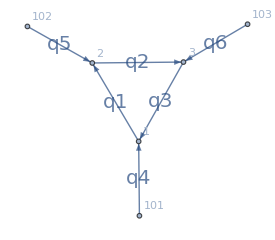

```mathematica
Tri1L=DirectedGraph[{
DirectedEdge[1,2,1],
DirectedEdge[2,3,2],
DirectedEdge[3,1,3],
DirectedEdge[101,1,4],
DirectedEdge[102,2,5],
DirectedEdge[103,3,6]
},VertexLabels->Automatic,EdgeLabels->Automatic];
Tri1L=AssignSignatures[Tri1L,masses-><|1->1,2->2,3->3|>,lmb->{3}];
Tri1L=DirectedGraph[Tri1L,VertexLabels->Automatic,ImageSize->275,GraphLayout->"HighDimensionalEmbedding",
EdgeLabels->Table[e->Style[("q"<>ToString[((e/.{DirectedEdge[_,_,props_]:>props})["id"])]),FontSize->20],{e,EdgeList[Tri1L]}]]
```

```mathematica
Tri1Lnumerics=GenerateRandomSample[Tri1L,Seed->1];
(*
Tri1Lnumerics={
k1->Evaluate[k1/.Tri1Lnumerics],
p1->Evaluate[p1/.Tri1Lnumerics],
p2->Evaluate[p2/.Tri1Lnumerics],
p3->Evaluate[p3/.Tri1Lnumerics],
p1E->0,
p2E->0,
p3E->0
}
*)
```

```mathematica
(
(ComputeSubtractionTerm[
<|
"cFFexpr"->ConvertCFFFormat[CrossFreeFamilyLTD[Tri1L,ConvertToNormalisedFormat->True],Tri1L],
"num"->1,
"graph"->Tri1L,
"dots"-><||>
|>,
Tri1Lnumerics]/.{λ->1})
-
(ComputeSubtractionTerm[
<|
"cFFexpr"->ConvertCFFFormat[CrossFreeFamilyLTD[Tri1L,ConvertToNormalisedFormat->True],Tri1L],
"num"->(SP4[q[3],q[3]]-3^2),
"graph"->Tri1L,
"dots"-><|3->2|>
|>,
Tri1Lnumerics]/.{λ->1})
)
```

<|{-1,-1,1}→0,{-1,1,-1}→0,{-1,1,1}→0,{1,-1,-1}→0,{1,-1,1}→0,{1,1,-1}→0|>

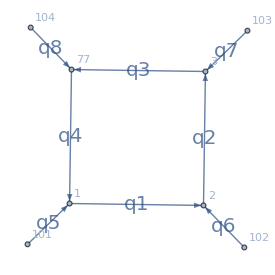

```mathematica
Box1L=DirectedGraph[{
DirectedEdge[1,2,1],
DirectedEdge[2,3,2],
DirectedEdge[3,77,3],
DirectedEdge[77,1,4],
DirectedEdge[101,1,5],
DirectedEdge[102,2,6],
DirectedEdge[103,3,7],
DirectedEdge[104,77,8]
},VertexLabels->Automatic,EdgeLabels->Automatic];
Box1L=AssignSignatures[Box1L,masses-><|1->1,2->2,3->3,4->3|>,lmb->{4}];
Box1L=DirectedGraph[Box1L,VertexLabels->Automatic,ImageSize->275,GraphLayout->"HighDimensionalEmbedding",
EdgeLabels->Table[e->Style[("q"<>ToString[((e/.{DirectedEdge[_,_,props_]:>props})["id"])]),FontSize->20],{e,EdgeList[Box1L]}]]
```

```mathematica
Dataset[Association[Table[((#["id"]->#["sig"])&)[e/.{DirectedEdge[_,_,props_]:>props}],{e,EdgeList[Tri1L]}]]]
Dataset[Association[Table[((#["id"]->#["sig"])&)[e/.{DirectedEdge[_,_,props_]:>props}],{e,EdgeList[Box1L]}]]]
```

```mathematica
Box1Lnumerics=Join[Tri1Lnumerics,{p4->{0,0,0},p4E->0}]
```

{k1→{2/3,3/5,5/7},p1→{7/11,11/13,13/17},p2→{17/19,19/23,23/29},p1E→29/31,p2E→31/37,p3→{-320/209,-500/299,-768/493},p3E→-2034/1147,p4→{0,0,0},p4E→0}

```mathematica
{
Total[Values[(ComputeSubtractionTerm[
<|
"cFFexpr"->ConvertCFFFormat[CrossFreeFamilyLTD[Box1L,ConvertToNormalisedFormat->True],Box1L],
"num"->1,
"graph"->Box1L,
"dots"-><||>
|>,
Box1Lnumerics]/.{λ->1})]]
,
Total[Values[(ComputeSubtractionTerm[
<|
"cFFexpr"->ConvertCFFFormat[CrossFreeFamilyLTD[Tri1L,ConvertToNormalisedFormat->True],Tri1L],
"num"->1,
"graph"->Tri1L,
"dots"-><|3->2|>
|>,
Tri1Lnumerics]/.{λ->1})]]
}//N
(%⟦1⟧)/(%⟦2⟧)
```

{0.0000399946,-0.0000399946}

-1.